```mathematica
<<"PlotLegends`"
```

```mathematica
<< "/Users/oliviercroissant/Documents/Math/BS.m"
```

```mathematica
Off[FindRoot::"precw",FindRoot::"lstol"]
```

```mathematica
<<"ErrorBarPlots`"
```

```mathematica
Nd[x_]:=N[(Erf[x/(√2)]+1)/2,40]
```

```mathematica
BS1[f_,k_,t_,v_]:=f NormalDis[(Log[f/k]+(v^2 t)/2)/(v √t)]-k NormalDis[(Log[f/k]-(v^2 t)/2)/(v √t)]
```

```mathematica
BS[f_,k_,t_,v_]:= f  Nd[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  Nd[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
PhiVol[m_,u_]:=Exp[m] Nd[m/u+u/2]-Nd[m/u-u/2]
```

```mathematica
Off[FindRoot::"precw",FindRoot::"reged"]
```

```mathematica
ImpVolBS[F_,K_,t_,discount_,opt_]:=Module[{o=opt/(K  discount),m=Log[F/K],ss},
ss=FindRoot[PhiVol[m,u]==o,{u,0.2,0.0001,15.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss[[1,2]]/Sqrt[t]]
```

```mathematica
Developpement a la monnaie
```

```mathematica
Justification de la relation entre θ et κ dans Hagan
```

```mathematica
Simplify[Series[1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2))/(f-K)Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν (1-2 ν ρ z+ν^2 z^2)^(1/4)] /. z->(f^(1-β)-K^(1-β))/(α (1-β)),{f,K,2}],K>0]
```

(K^(-2 (1+β)) (K^(2 β) α^2 (-2+β) β+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2))) (f-K)^2)/(24 α^2)+O[f-K]^3

```mathematica
Option Directe cas exact
```

```mathematica
Simplify[Series[ Log[f/K]/z ξ/(ν x)//.{ξ->ν(f^(1-β)-K^(1-β))/(α (1-β)), z->(f^(1-β)-K^(1-β))/(α (1-β)),x->Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν},{f,K,1}],K>0]
```

K^(-1+β) α+((K^β α (-1+β)-K ν ρ) (f-K))/(2 K^2)+O[f-K]^2

```mathematica
Simplify[Series[ ((1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2))/(f-K)Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν (1-2 ν ρ z+ν^2 z^2)^(1/4)]-Log[(Log[f/K] √(f K))/(f-K)])/x^2)//.{ξ->ν(f^(1-β)-K^(1-β))/(α (1-β)), z->(f^(1-β)-K^(1-β))/(α (1-β)),x->Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν},{f,K,1}],K>0]
```

(K^(2 β) α^2 (-1+β)^2+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2)))/(24 K^2)+(K^(-3-β) (K^(3 β) α^3 (-1+β)^3-K^(1+2 β) α^2 (-1+β)^2 ν ρ-3 K^3 ν^2 ρ (2 b1 α ρ+ν (-1+ρ^2))) (f-K))/(24 α)+O[f-K]^2

```mathematica
Option Directe cas arithmetic
```

```mathematica
Simplify[Series[ Log[f/K]/z ξ/(ν x)//.{ξ->ν/α((f+K)/2)^(1-β)Log[f/K], z-> 1/α(f-K)/((f+K)/2)^β,x->Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν},{f,K,1}],K>0]
```

K^(-1+β) α+((K^β α (-1+β)-K ν ρ) (f-K))/(2 K^2)+O[f-K]^2

```mathematica
Option Hagan cas Exact
```

```mathematica
Simplify[Series[α/(f K)^((1-β)/2) z/x//.{ξ->ν(f^(1-β)-K^(1-β))/(α (1-β)), z->(f^(1-β)-K^(1-β))/(α (1-β)),x->Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν},{f,K,1}],K>0]
```

K^(-1+β) α+((K^β α (-1+β)-K ν ρ) (f-K))/(2 K^2)+O[f-K]^2

```mathematica
Option Analytic cas Exact
```

```mathematica
Simplify[Series[(f-K)/(2 √(2π))1/x//.{ξ->ν(f^(1-β)-K^(1-β))/(α (1-β)), z->(f^(1-β)-K^(1-β))/(α (1-β)),x->Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν},{f,K,1}],K>0]
```

(K^β α)/(2 √(2 π))+((K^β α β-K ν ρ) (f-K))/(4 K √(2 π))+O[f-K]^2

```mathematica
Universal Function
```

```mathematica
SABRVol[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_},K_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav,v},
If[favmethod=="Strike",
fav=K;];
If[favmethod=="Arithmetic",
fav=(f+K)/2;];
If[favmethod=="Geometric",
fav=√(f K)];
If[favmethod=="Forward",
fav=f];
If[zmethod=="Exact",
 z=(f^(1-β)-K^(1-β))/(α (1-β));];
If[zmethod=="Geometric",
 z=1/α(f K)^((1-β)/2)Log[f/K];];
If[zmethod=="Arithmetic",
 z=1/α(f-K)/fav^β];
If[zetamethod=="Exact",
 ξ=ν(f^(1-β)-K^(1-β))/(α (1-β))];
If[zetamethod=="Geometric",
 ξ=ν/α(fav)^(1-β)Log[f/K]];
If[zetamethod=="Arithmetic",
 ξ=ν/α(f-K)/fav^β];
b1=β fav^(β-1);
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
If[method=="Directe",
sig=Log[f/K]/z ξ/(ν x)(1-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2))^(-1/2);
  result=sig;];
If[method=="NormaleHagan",
sig=α/(f K)^((1-β)/2) z/x  (1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T) / (1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
  result=sig;];
If[method=="MetaNormale",
γ1=β/fav;γ2=(β(β-1))/fav^2;
sig=Log[f/K]/z*ξ/(ν x)*(1+(((2γ2-γ1^2+1/fav^2)α^2)/(24 fav^(-2β))+(ρ α ν γ1)/(4 fav^-β)+1/24 ν^2 (2-3 ρ^2))T);

   result=sig;];
If[method=="SuperNormale",

sigN=(f-K)/z*ξ/(ν x)*(1+((-β(2-β)α^2)/(24 fav^(2-2β))+(ρ α ν β)/(4 fav^(1-β))+1/24 ν^2 (2-3 ρ^2))T);
sig=sigN/(√(f K)) (1+1/24(1-1/120 Log[f/K]^2)T sigN^2/(f K))/(1+1/24 Log[f/K]^2+1/1920 Log[f/K]^4);
  result=sig];
If[method=="SABR Type",
b=x;
a=√-κ;
  (*(call=N[Max[f-K,0]+(f-K)/(2 √(2π))ⅇ^θ/x ∫_0^T (ⅇ^(-b^2/(2v)-a^2 v))/(√v)ⅆv ];*)
result=ImpVolBS[f,K,T,1,call]];
If[method=="SABR Type Analytic",
b=Abs[x];
a=√-κ;
call=Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))];
result=VolImpliciteBS[f,K,T,1,call];];
result];
```

```mathematica
SABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_},K_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},
If[favmethod=="Strike",
fav=K;];
If[favmethod=="Arithmetic",
fav=(f+K)/2;];
If[favmethod=="Geometric",
fav=√(f K)];
If[favmethod=="Forward",
fav=f];
If[zmethod=="Exact",
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β));Dzk=-K^-β/α,z=Log[f]/α-Log[K]/α;Dzk=-1/(K α)]];
If[zmethod=="Geometric",
 z=1/α(f K)^((1-β)/2)Log[f/K];Dzk=-(f (f K)^(-1/2-β/2) (2+(-1+β) Log[f/K]))/(2 α)];
If[zmethod=="Arithmetic",
 z=1/α(f-K)/fav^β];
If[zetamethod=="Exact",
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)]];
If[zetamethod=="Geometric",
 ξ=ν/α(fav)^(1-β)Log[f/K]];
If[zetamethod=="Arithmetic",
 ξ=ν/α(f-K)/fav^β];
b1=β fav^(β-1);
If[z==0,x=1,
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν];
If[z==0 ,θ=0,
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z]];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
If[method=="Directe",
If[Abs[z]≤10^-4,sig=K^(-1+β) α(1-2 T(K^(2 β) α^2 (-1+β)^2+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2)))/(24 K^2))^(-1/2),
sig=Log[f/K]/z ξ/(ν x)(1-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2))^(-1/2)];
  result={sig,BS[f,K,T,sig]};];
If[method=="NormaleHagan",

If[z==0,sig=K^(-1+β) α(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T) / (1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920),
sig=α/(f K)^((1-β)/2) z/x  (1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T) / (1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920)];
  result={sig,BS[f,K,T,sig]};];
If[method=="MetaNormale",
γ1=β/fav;γ2=(β(β-1))/fav^2;
sig=Log[f/K]/z*ξ/(ν x)*(1+(((2γ2-γ1^2+1/fav^2)α^2)/(24 fav^(-2β))+(ρ α ν γ1)/(4 fav^-β)+1/24 ν^2 (2-3 ρ^2))T);

   result={sig,BS[f,K,T,sig]};];
If[method=="SuperNormale",

sigN=(f-K)/z*ξ/(ν x)*(1+((-β(2-β)α^2)/(24 fav^(2-2β))+(ρ α ν β)/(4 fav^(1-β))+1/24 ν^2 (2-3 ρ^2))T);
sig=sigN/(√(f K)) (1+1/24(1-1/120 Log[f/K]^2)T sigN^2/(f K))/(1+1/24 Log[f/K]^2+1/1920 Log[f/K]^4);
  result={sig,BS[f,K,T,sig]}];
If[method=="SABR Type Analytic",
b=Abs[x];
a=√-κ;
If[z==0,call=N[(K^β α)/(2 √(2 π))Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]],
call=N[Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]]];
result={ImpVolBS[f,K,T,1,call],call};];
If[method=="DirecteSimple",

sig=(Log[f/K] ξ)/(x z ν);
  result={sig,BS[f,K,T,sig]}];

result];
```

```mathematica
Implemente le strike cuting de natexis sous deux flavour
```

```mathematica
SABRVol[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_,{Tanh,zerocuterKb_,αp_}},K1_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},K=UnitStep[K1-zerocuterKb]K1+(UnitStep[zerocuterKb-K1]) zerocuterKb(1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)]);
SABRVol[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K1,T]]
```

```mathematica
SABRVol[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_,{Exponential,ϵ_}},K1_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},
K=K1+ϵ ⅇ^(-K1/ϵ);
SABRVol[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K1,T]]
```

```mathematica
SABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_,{Tanh,zerocuterKb_,αp_}},K1_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},K=UnitStep[K1-zerocuterKb]K1+(UnitStep[zerocuterKb-K1]) zerocuterKb(1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)]);
SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K1,T]]
```

```mathematica
SABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_,{Exponential,ϵ_}},K1_,T_]:=
Module[{z,Dzk,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,fav},
K=K1+ϵ ⅇ^(-K1/ϵ);
SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K1,T]]
```

```mathematica
SABROptionDistribution[f_,α_,β_,ρ_,ν_,Meth_,K_,T_]:=Module[{shift=0.00001},1-(-SABROption[f,α,β,ρ,ν,Meth,K+shift,T][[2]]+SABROption[f,α,β,ρ,ν,Meth,K-shift,T][[2]])/(2shift)]
```

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.0001,
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Tanh,0.05,1.5}}},
{SABROptionDistribution[f,α,β,ρ,ν,Meth1,K,T],SABROptionDistribution[f,α,β,ρ,ν,Meth2,K,T]}]
```

{0.000489716,0.00012226}

```mathematica
SABROptionQuantile[f_,α_,β_,ρ_,ν_,Meth_,p_,T_]:=Module[{x,ss},ss=FindRoot[SABROptionDistribution[f,α,β,ρ,ν,Meth,x,T]==p,{x,f*1.1,10^(-100),1.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];
ss[[1,2]]]
```

```mathematica
SABROptionQuantile[f_,α_,β_,ρ_,ν_,Meth_,p_,T_]:=Module[{x,ss},ss=NewtonFindRoot[(SABROptionDistribution[f,α,β,ρ,ν,Meth,#,T]-p)&,f*1.1,0.00001,10^(-10),200]]
```

```mathematica
(* je suis obligé d'utiliser NewtonFindRoot parce que FindRoot ne marche pas ! *)
```

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,p=0.001,
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Exponential,0.01}}},
{SABROptionQuantile[f,α,β,ρ,ν,Meth1,p,T],SABROptionQuantile[f,α,β,ρ,ν,Meth2,p,T]}]
```

{{0.000762313,9,2.56717×10^-12},{0.00303062,9,2.62292×10^-11}}

```mathematica
derivation symbolique par rapport a K (solution du pb du au strike cuter de natexis)
```

```mathematica
BS[f_,k_,t_,v_]:= f  Nd[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  Nd[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
DerKSABROption[method_]:=Block[{SABRfunc,SABRder,SABRder2,zerocuterKb,αp,l,f,α,β,ρ,ν,K,T,ϵ},
l=Length[method];
If[l==4,SABRfunc=BS[f,K,T,SABRVol[f,α,β,ρ,ν,method,K,T]];
SABRder=D[SABRfunc, K];
ReplacePart[{{f,α,β,ρ,ν,K,T},SABRder},Function,0],If[l==5&&method⟦5,1⟧===Exponential,
ϵ=method⟦5,2⟧;
SABRfunc=SABRVol[f,α,β,ρ,ν,Take[method,4],K+ϵ ⅇ^(-K/ϵ),T];
SABRder=D[BS[f,K,T,SABRfunc], {K,1}];
ReplacePart[{{f,α,β,ρ,ν,K,T},SABRder},Function,0],
If[l==5&&method⟦5,1⟧===Tanh,
zerocuterKb=method⟦5,2⟧;
αp=method⟦5,3⟧;
SABRfunc1=SABRVol[f,α,β,ρ,ν,Take[method,4],K1,T];
SABRder1=D[BS[f,K1,T,SABRfunc1], {K1,1}];
SABRfunc2=SABRVol[f,α,β,ρ,ν,Take[method,4],K,T]/.{K-> zerocuterKb (1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)])};
SABRder2=(D[BS[f,K1,T,SABRfunc2], {K1,1}])/.{K-> zerocuterKb (1+αp Tanh[(K1-zerocuterKb)/(αp zerocuterKb)])};

SABRder=(UnitStep[K1-zerocuterKb]SABRder1+UnitStep[zerocuterKb-K1] SABRder2);
ReplacePart[{{f,α,β,ρ,ν,K1,T},SABRder},Function,0]]]]]
```

```mathematica
Module[{Meth1={"NormaleHagan","Geometric","Geometric","Geometric"},
Meth2={"Directe","Exact","Exact","Arithmetic"}},
ff1=DerKSABROption[Meth1];
ff2=DerKSABROption[Meth2];
{ff1[0.05,0.11,0.7,-0.5,0.2,0.04,1],ff2[0.05,0.11,0.7,-0.5,0.2,0.04,1]}]
```

{-0.765083,-0.764972}

```mathematica
Module[{Meth1={"NormaleHagan","Geometric","Geometric","Geometric"},
Meth2={"Directe","Exact","Exact","Arithmetic"}},
ff1=DerKSABROption[Meth1]]
```

```mathematica
Module[{Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Tanh,0.05,1.5}}},
ff1=DerKSABROption[Meth1];
ff2=DerKSABROption[Meth2];
{ff1[0.05,0.11,0.7,-0.5,0.2,0.0354,1],ff2[0.05,0.11,0.7,-0.5,0.2,0.0354,1]}]
```

{-0.862716,-0.862785}

```mathematica
Module[{
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Exponential,0.05}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Exponential,0.05}}},
ff1=DerKSABROption[Meth1];
ff2=DerKSABROption[Meth2];
{ff1[0.05,0.11,0.7,-0.5,0.2,0.0354,1],ff2[0.05,0.11,0.7,-0.5,0.2,0.0354,1]}]
```

{-0.896016,-0.895831}

```mathematica
Solution of the partial differential equation
```

```mathematica
(* Q[x_,w_]:=1/(√(2π w))ⅇ^(-x^2/(2t)+∫_0^w κ[s]ⅆs) *)
```

```mathematica
(* FullSimplify[Q^(0,1)[x,t]-1/2 Q^(2,0)[x,t]-κ[t]Q[x,t]] *)
```

```mathematica
Study of the integral to perform
```

```mathematica
Simplify[Series[(√π)/(4a)(ⅇ^(- 2a  b)  (1-ⅇ^(4  a b)+ⅇ^(4  a b) Erf[b/x+a x]-Erf[b/x-a x])),{a,0,2}]]
```

(-b √π+ⅇ^(-b^2/x^2) x+b √π Erf[b/x])+1/3 (-ⅇ^(-b^2/x^2) (2 b^3 ⅇ^(b^2/x^2) √π-2 b^2 x+x^3)+2 b^3 √π Erf[b/x]) a^2+O[a]^3

```mathematica
Simplify[Series[(√π)/(4a)(ⅇ^(- 2a  b)  (1-ⅇ^(4  a b)+ⅇ^(4  a b) Erf[b/x+a x]-Erf[b/x-a x])),{a,0,4}]]
```

(-b √π+ⅇ^(-b^2/x^2) x+b √π Erf[b/x])+1/3 (-ⅇ^(-b^2/x^2) (2 b^3 ⅇ^(b^2/x^2) √π-2 b^2 x+x^3)+2 b^3 √π Erf[b/x]) a^2+1/30 ⅇ^(-b^2/x^2) (-4 b^5 ⅇ^(b^2/x^2) √π+4 b^4 x-2 b^2 x^3+3 x^5+4 b^5 ⅇ^(b^2/x^2) √π Erf[b/x]) a^4+O[a]^5

```mathematica
GIntegral[a_,b_,x_]:=Module[{},Print["a=",a," b=",b];NIntegrate[Exp[-a^2 x1^2-b^2/x1^2],{x1,0,x}]]
```

```mathematica
GIntegralReduced[b_,x1_]:= b √π If[x1>0,Erf[b/x1]-1,Erf[b/x1]+1]+ⅇ^(-b^2/x1^2) x1
```

```mathematica
GIntegralAnalytical[a1_,b1_,x1_]:=Module[{a,b,x},
x=Abs[x1];
b=Abs[b1];
a=Abs[a1];
Re[If[Abs[a]>0.001,Sign[x1]((√π)/(4a)(ⅇ^(- 2a  b)  (1-ⅇ^(4  a b)+ⅇ^(4  a b) Erf[b/x+a x]-Erf[b/x-a x]))),
Sign[x1](-b √π+ⅇ^(-b^2/x^2) x+b √π Erf[b/x])+1/3 (-ⅇ^(-b^2/x^2) (2 b^3 ⅇ^(b^2/x^2) √π-2 b^2 x+x^3)+2 b^3 √π Erf[b/x]) a^2+1/30 ⅇ^(-b^2/x^2) (-4 b^5 ⅇ^(b^2/x^2) √π+4 b^4 x-2 b^2 x^3+3 x^5+4 b^5 ⅇ^(b^2/x^2) √π Erf[b/x]) a^4
]]]
```

```mathematica
Module[{a=-0.1,b=-0.2,x=-0.4},{GIntegral[a,b,x],GIntegralAnalytical[a,b,x],GIntegralAnalytical[a,b,-x]}]
```

{-0.141414,-0.141414,0.141414}

```mathematica
GIntegralAnalytical4[a_,b_,T_]:=Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]
```

```mathematica
Module[{a=0.1,b=0.2,x=0.4},{GIntegral[a,b,x],GIntegralAnalytical[a,b,x],GIntegralAnalytical4[√2 a,Abs[b],x^2/2]/√2}]
```

a=0.1 b=0.2

{0.141414,0.141414,0.141414}

```mathematica
Module[{a=0.15ⅈ,b=0.23,x=0.42},{√2 GIntegral[a/√2,b,√(2x)],√2 GIntegralAnalytical[a/√2,b,√(2x)],GIntegralAnalytical4[a,b,x]}]
```

a=0.106066 ⅈ b=0.23

{0.803931,0.796898,0.803931}

```mathematica
Fonctions utiles
```

```mathematica
Performs the integral : ∫_0^x ⅇ^(-a^2 s^2-b^2/s^2)ⅆs=GIntegralAnalytical3[a,b,x]
```

```mathematica
Implementation of GIntegralAnalytical  using Numerical integration
```

```mathematica
GIntegral[a_,b_,x_]:=NIntegrate[Exp[-a^2 x1^2-b^2/x1^2],{x1,0,x}]
```

```mathematica
Implementation of GIntegralAnalytical  using ERF function
```

```mathematica
GIntegralAnalytical[a1_,b1_,x1_]:=Module[{a,b,x},
x=Abs[x1];
b=Abs[b1];
a=Abs[a1];
Re[If[Abs[a]>0.001,Sign[x1]((√π)/(4a)(ⅇ^(- 2a  b)  (1-ⅇ^(4  a b)+ⅇ^(4  a b) Erf[b/x+a x]-Erf[b/x-a x]))),
Sign[x1](-b √π+ⅇ^(-b^2/x^2) x+b √π Erf[b/x])+1/3 (-ⅇ^(-b^2/x^2) (2 b^3 ⅇ^(b^2/x^2) √π-2 b^2 x+x^3)+2 b^3 √π Erf[b/x]) a^2+1/30 ⅇ^(-b^2/x^2) (-4 b^5 ⅇ^(b^2/x^2) √π+4 b^4 x-2 b^2 x^3+3 x^5+4 b^5 ⅇ^(b^2/x^2) √π Erf[b/x]) a^4
]]]
```

```mathematica
Implementation of GIntegralAnalytical  using NormalCDF function
```

```mathematica
GIntegralAnalytical1[a1_,b1_,x1_]:=Module[{a,b,x},
x=Abs[x1];
b=Abs[b1];
a=Abs[a1];
Re[If[Abs[a]>0.001,Sign[x1](ⅇ^(-2 a b) √π (1-ⅇ^(4 a b)-NormalCDF[√2 (b/x-a x)]+ⅇ^(4 a b) NormalCDF[√2 (b/x+a x)]))/(2 a),
Sign[x1]/30 (ⅇ^(-b^2/x^2) x (30+10 a^2 (2 b^2-x^2)+a^4 (4 b^4-2 b^2 x^2+3 x^4))+4 b (15+10 a^2 b^2+2 a^4 b^4) √π (-1+NormalCDF[(√2 b)/x]))
]]]
```

```mathematica
Implementation of GIntegralAnalytical  using NormalDis function  but with           GIntegralAnalytical2[a^2,b,x]==GIntegralAnalytical3[a,b,x]
```

```mathematica
GIntegralAnalytical2[a2_,b1_,x1_]:=Module[{a,b,x,a0,b0,c0,d0,e0,argERF,ERF},
x=Abs[x1];
b=Abs[b1];
argERF=b/x √2;
ERF=2NormalDis[b/x √2]-2;
a0=ⅇ^(-b^2/x^2) x+b √π ERF;
b0=ⅇ^(-b^2/x^2) (2 b^2 x-x^3)+2 b^3 √π ERF;
c0=ⅇ^(-b^2/x^2) (4 b^4 x-2 b^2 x^3+3 x^5)+4 b^5  √π ERF;
d0=ⅇ^(-b^2/x^2) (8 b^6 x-4 b^4 x^3+6 b^2 x^5-15 x^7)+8 b^7 √π ERF;
e0=ⅇ^(-b^2/x^2) (16 b^8 x-8 b^6 x^3+12 b^4 x^5-30 b^2 x^7+105 x^9)+16 b^9  √π ERF ;
Sign[x1](a0+1/3 b0  a2+1/30 c0 a2^2+1/630 d0 a2^3+1/22680 e0 a2^4 )];
```

```mathematica
Implementation of GIntegralAnalytical  using NormalDis function
```

```mathematica
GIntegralAnalytical3[a1_,b1_,x1_]:=Module[{a,b,x,a0,b0,c0,d0,e0},
x=Abs[x1];
b=Abs[b1];
a=a1;
ERF=(2NormalDis[b/x √2]-1)-1;
a0=ⅇ^(-b^2/x^2) x+b √π ERF;
b0=ⅇ^(-b^2/x^2) (2 b^2 x-x^3)+2 b^3 √π ERF;
c0=ⅇ^(-b^2/x^2) (4 b^4 x-2 b^2 x^3+3 x^5)+4 b^5  √π ERF;
d0=ⅇ^(-b^2/x^2) (8 b^6 x-4 b^4 x^3+6 b^2 x^5-15 x^7)+8 b^7 √π ERF;
e0=ⅇ^(-b^2/x^2) (16 b^8 x-8 b^6 x^3+12 b^4 x^5-30 b^2 x^7+105 x^9)+16 b^9  √π ERF ;
Sign[x1](a0+1/3 b0  a^2+1/30 c0 a^4+1/630 d0 a^6+1/22680 e0 a^8 )];
```

```mathematica
Module[{a=0.1,b=-0.8,x=0.4},{GIntegral[a,b,x],GIntegralAnalytical[a,b,x],GIntegralAnalytical1[a,b,x],GIntegralAnalytical2[a^2,b,x],GIntegralAnalytical3[a,b,x]}]
```

{0.000692452,0.000692452,7.55193 (-0.377128+Re[-NormalCDF[2.77186]+1.37713 NormalCDF[2.885]]),0.000692452,0.000692452}

```mathematica
Module[{a=√-0.010727040262854,b=-1.8122261909661/(√2),x=1.0},{SetPrecision[GIntegral[a,b,x],12],SetPrecision[GIntegralAnalytical[a,b,x],12],SetPrecision[GIntegralAnalytical3[a,b,x],12],SetPrecision[GIntegralAnalytical2[a^2,b,x],12]}]
```

{0.0349830696349+0. ⅈ,0.034413631202,0.0349830696348+0. ⅈ,0.0349830696348+0. ⅈ}

```mathematica
SetPrecision[2.3659625868524/(√2),15]
```

1.672988189197

```mathematica
GIntegralAnalytical2[-0.010727040262854,-1.8122261909661/(√2),√1.0]
```

0.0349831

```mathematica
Exemple :
```

```mathematica
Module[{α=0.11,β=0.7,ρ=-0.5,ν=0.2,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",f=0.05,K=0.04,T=1},SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T]]
```

{0.290373314386350171724873045547,0.0116395}

```mathematica
Module[{α=0.11,β=0.7,ρ=-0.5,ν=0.2,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",f=0.05,K=0.04,T=1},SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod,{Tanh,0.00001,1.}},K,T]]
```

{0.290373314386350171724873045547,0.0116395}

```mathematica
DigitalSABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetavmethod_,b1method_},K_,T_]:=Module[{shift=0.0001 f},-(SABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K+shift,T][[2]]-SABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K-shift,T][[2]])/(2shift)]
```

```mathematica
DistributionSABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetavmethod_,b1method_},K_,T_]:=Module[{},If[K>f/200,1-DigitalSABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K,T],0]]
```

```mathematica
DistributionSABROptionInverse[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetavmethod_,b1method_},p_,T_]:=Module[{x,ss},ss=FindRoot[DistributionSABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},x,T]==p,{x,f*1.1,10^(-100),1.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];
ss[[1,2]]]
```

```mathematica
n1=DistributionSABROption[0.05,0.11,0.7,-0.5,0.2,{"Directe","Exact","Exact","Arithmetic"},0.06,1]
```

0.778048

```mathematica
DistributionSABROptionInverse[0.05,0.11,0.7,-0.5,0.2,{"Directe","Exact","Exact","Arithmetic"},n1,1]
```

0.060000000000008504648625353575

```mathematica
DensitySABROption[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetavmethod_,b1method_},K_,T_]:=Module[{shift=0.0001 f},
If[K>f/200,(SABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K-shift,T][[2]]-2SABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K,T][[2]]+
SABROption[f,α,β,ρ,ν,{method,zmethod,zetavmethod,b1method},K+shift,T][[2]])/(shift^2),
0]]
```

```mathematica
PlotVolCase[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,b1method_},{Kmin_,Kmax_},T_]:=Module[{},
Off[FindRoot::"lstol",FindRoot::"precw",FindRoot::"reged"];
Plot[
SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,b1method},K,T][[1]]
,{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0]}]];
```

```mathematica
PlotDensityCase[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,b1method_},{Kmin_,Kmax_},T_]:=Module[{},
Off[FindRoot::"lstol",FindRoot::"precw",FindRoot::"reged"];
Plot[
DensitySABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,b1method},K,T],{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0]}]];
```

```mathematica
PlotDigitalCase[f_,α_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,b1method_},{Kmin_,Kmax_},T_]:=Module[{},
Off[FindRoot::"lstol",FindRoot::"precw",FindRoot::"reged"];
Plot[
DigitalSABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,b1method},K,T]
,{K,Kmin,Kmax},PlotRange->{0,1.2},
PlotStyle->{RGBColor[1,0,0]}]];
```

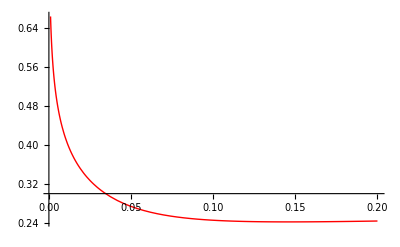

```mathematica
PlotVolCase[0.04041212,0.11,0.7,-0.3,0.2,{"Directe","Exact","Exact","Arithmetic"},{0.001,0.2},1.5]
```

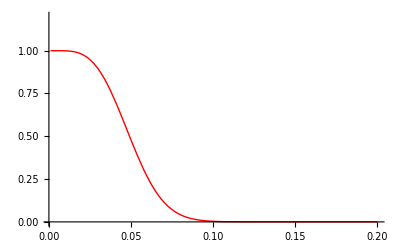

```mathematica
PlotDigitalCase[0.05,0.11,0.7,-0.5,0.2,{"MetaNormale","Exact","Arithmetic","Arithmetic"},{0.001,0.2},1.5]
```

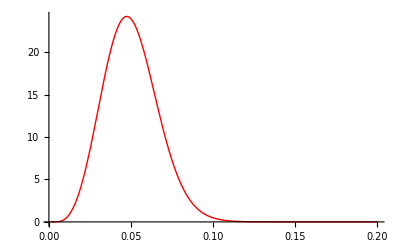

```mathematica
PlotDensityCase[0.05,0.11,0.7,-0.5,0.2,{"MetaNormale","Exact","Arithmetic","Arithmetic"},{0.001,0.2},1.5]
```

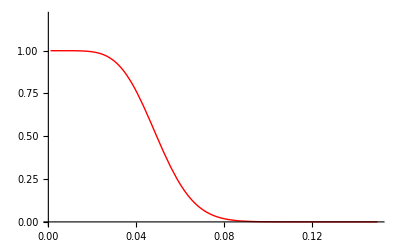

```mathematica
PlotDigitalCase[0.05,0.11,0.7,-0.5,0.2,{"Directe","Exact","Exact","Arithmetic"},{0.001,0.15},1]
```

```mathematica
SABR Simplifié
```

```mathematica
SimplifiedSABROption[f_,α_,β_,ρ_,ν_,K_,T_,printflag_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,intrinsec},
fav=(f+K)/2;
 z=(f^(1-β)-K^(1-β))/(α (1-β));
 ξ=ν(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
I0=√(1-2 ν ρ z+ν^2 z^2);
B0Bαz=(K f)^β;
f1overf0=ⅇ^(1/4 α b1 ν ρ z^2);
intrinsec=Max[f-K,0];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
If[printflag>0,Print["call: x=",x," f1overf0=",f1overf0," √B0Bαz=",√B0Bαz," I0=",I0," κ=",κ," intrinsec=",intrinsec]];
  call=N[intrinsec+f1overf0/(√(2π))α  √B0Bαz √I0 Re[GIntegralAnalytical3[√-κ,Abs[x]/(√2),√T]]];
result={ImpVolBS[f,K,T,1,call],call};
result];
```

```mathematica
SABR Hagan quick!
```

```mathematica
SABRHaganVol[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,x,Effetmat},z=(f^(1-β)-K^(1-β))/(α (1-β));
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
Effetmat=(1+(1/24 α^2 (1-β)^2 (f K)^(-1+β)+1/4 α β (f K)^(1/2 (-1+β)) ν ρ+1/24 ν^2 (2-3 ρ^2)) T)/(1+1/24 (1-β)^2 Log[f/K]^2+((1-β)^4 Log[f/K]^4)/1920);
If[z==0,K^(-1+β) α Effetmat,
α/(f K)^((1-β)/2) z/x  Effetmat  ]]
```

```mathematica
SABRHaganOption[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{vol},
vol=  SABRHaganVol[f,α,β,ρ,ν,K,T];
BS[f,K,T,vol ]]
```

```mathematica
SABRHaganDensity[f_,K_,α_,β_,ρ_,ν_,T_]:=Module[{v0,v1,v2,shift},
shift=Min[K,f]/10000;
v0= SABRHaganOption[f,α,β,ρ,ν,K,T];
v1= SABRHaganOption[f,α,β,ρ,ν,K+shift,T];
v2= SABRHaganOption[f,α,β,ρ,ν,K-shift,T];
(v1+v2-2v0)/(shift^2)]
```

```mathematica
SABROptionHagan[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{vol},
vol=  SABRHaganVol[f,α,β,ρ,ν,K,T];
{vol,BS[f,K,T,vol ]}]
```

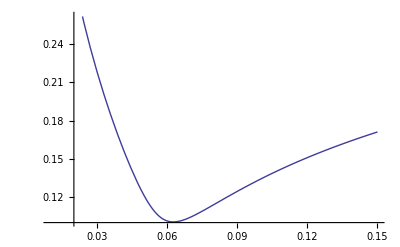

```mathematica
Module[{f=0.05,α=0.0248,T=17,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[SABRHaganVol[f,α,β,ρ,ν,K,T],{K,0.01,0.15}]]
```

```mathematica
SABR Analytic quick!
```

```mathematica
SABROptionAnalyticDistribution[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{shift=0.00001},(-SABROptionAnalyticOption[f,α,β,ρ,ν,K+shift,T]+SABROptionAnalyticOption[f,α,β,ρ,ν,K-shift,T])/(2shift)]
```

```mathematica
SABROptionAnalyticDensity[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{shift=0.00001},(SABROptionAnalyticOption[f,α,β,ρ,ν,K+shift,T]+SABROptionAnalyticOption[f,α,β,ρ,ν,K-shift,T]-2SABROptionAnalyticOption[f,α,β,ρ,ν,K,T])/(shift^2)]
```

```mathematica
SABROptionAnalyticQuantile[f_,α_,β_,ρ_,ν_,T_,prob_]:=Module[{K},If[prob>0.5,NewtonFindRoot[(SABROptionAnalyticDistribution[f,α,β,ρ,ν,#,T]-prob)&,0.8f,0.0001,0.0000001,100][[1]],
NewtonFindRoot[(SABROptionAnalyticDistribution[f,α,β,ρ,ν,#,T]-prob)&,1.2f,0.0001,0.0000001,100][[1]]]]
```

```mathematica
SABROptionAnalyticOption[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=0,
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z]];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
b=Abs[x];
a=√-κ;
If[z==0,call=(K^β α)/(2 √(2 π)) Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))],
  call=N[Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]]];
call];
```

```mathematica
SABROptionAnalytic[f_,α_,β_,ρ_,ν_,K_,T_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=0,
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z]];
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
b=Abs[x];
a=√-κ;
If[z==0,call=(K^β α)/(2 √(2 π)) Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))],
  call=N[Max[f-K,0]+(f-K)/(2 √(2π))E^θ/x Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]]];
result={ImpVolBS[f,K,T,1,call],call};

result];
```

```mathematica
SABROptionAnalytic[f_,α_,β_,ρ_,ν_,K_,T_,printflag_]:=
Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,I1,I0,I2,B0Bαz,f1overf0},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
I0=√(1+z  ν (z ν-2 ρ));I1=(z ν-ρ)/I0;I2=(1-ρ^2)/I0^3;
B0Bαz=(f K)^β;
f1overf0=ⅇ^(1/4 α b1 ν ρ z^2);
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
b=Abs[x];
a=√-κ;
If[printflag>0,Print["SABROptionAnalytic: z=",SetPrecision[z,12]," x=",SetPrecision[x,12]," κ=",SetPrecision[κ,12]," b1=",SetPrecision[b1,12]," I0=",SetPrecision[I0,12]," f1overf0=",SetPrecision[f1overf0,12]]];
If[printflag>0,Print["SABROptionAnalytic: α^2/K^2=",SetPrecision[(α^2 (-2+β) β K^(2 β))/K^2,12]," (6 α β SuperscriptBox[K, β] ν ρ)/K=",SetPrecision[(6 α β K^β ν ρ)/K,12]," ν^2 (2-3 ρ^2)=",SetPrecision[ν^2 (2-3 ρ^2),12]]];
If[printflag>0,Print["SABROptionAnalytic: 1/2Re[(1/(2 a)(ⅇ^(-SqrtBox[2] a b) √π (1-ⅇ^(2 SqrtBox[2] a b)+ⅇ^(2 SqrtBox[2] a b) Erf[b/(√2)+a √T]-Erf[(√2)/(2 SqrtBox[T])])))]]=",SetPrecision[1/2 Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))],12]]];
  call=N[Max[f-K,0]+α/(2 √(2π)) √I0 √B0Bαz f1overf0 Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]];
result={ImpVolBS[f,K,T,1,call],call};

result];
```

FindRoot::nlnum: The function value {-0.5\ (1.  + Erf[0.707107\ (-0.1 + Times[« 2 »])]) + 0.025\ (1.  + Erf[0.707107\ « 1 »])/K - 1.\ (Max[0., 0.05  - 1.\ K] + 0.0058636\ « 3 »\ Re[Power[« 2 »]\ « 1 »\ Plus[« 4 »]])/K} is not a list of numbers with dimensions {1} at {u} = {0.2}.

General::stop: Further output of FindRoot :: "nlnum" will be suppressed during this calculation.

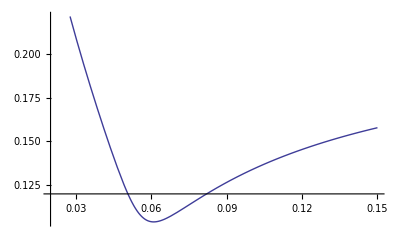

```mathematica
Module[{f=0.05,α=0.0248,T=17,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Plot[SABROptionAnalytic[f,α,β,ρ,ν,K,T,0][[1]],{K,0.02,0.15}]]
```

```mathematica
Module[{f=0.05,α=0.0248,T=17,β=0.5,ATMvol,ρ=-0.56,ν=0.45},
Table[{K,SABROptionAnalytic[f,α,β,ρ,ν,K,T,0][[1]]},{K,0.04,0.08,0.001}]]
```

{{0.04,0.162595266878214919367997936339},{0.041,0.158223610457598043924897434394},{0.042,0.153911932289931828502701811681},{0.043,0.149663393326496400946968615259},{0.044,0.145483119733244212691297779412},{0.045,0.141378712867354564465277594386},{0.046,0.137360883939098676855234039973},{0.047,0.133444218624843700501460025133},{0.048,0.129648055902154682328141948294},{0.049,0.125997426507484767643781016469},{0.05,0.122523933276163801384516909334},{0.051,0.119265970077288222023866639088},{0.052,0.116264262420093081568485532677},{0.053,0.113556032264456628538755685056},{0.054,0.111172242495989336506522998054},{0.055,0.109135057218974388285082090783},{0.056,0.107455652306869361836378285617},{0.057,0.106132964756661102216644880631},{0.058,0.105153834551729159773664665826},{0.059,0.104494640033682445358941847578},{0.06,0.104124095160621347576586468586},{0.061,0.104006572014038793886950693926},{0.062,0.104105267732838541703553683641},{0.063,0.104384726051954260695826729218},{0.064,0.104812511251178471575741198607},{0.065,0.105360077527700803139800888136},{0.066,0.106003013421896987372948570362},{0.067,0.106720875175791561902369760426},{0.068,0.107496794642778090174977903989},{0.069,0.108316995892032614308290404111},{0.07,0.109170304502082893339140054571},{0.071,0.110047694911404083357582542817},{0.072,0.11094189546311921396172301525},{0.073,0.111847055529438335339108385288},{0.074,0.112758471104790223478687544024},{0.075,0.113672361762804114808387850364},{0.076,0.114585690923200492490005970935},{0.077,0.11549602172118289079827181055},{0.078,0.116401401680159770932667053826},{0.079,0.117300270459216296344176242075},{0.08,0.118191385981466512331464794714}}

```mathematica
SABROptionAnalyticFromATMVol[f_,ATMvol_,β_,ρ_,ν_,K_,T_]:=
Module[{α,z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,call,I1,I0,I2,B0Bαz,f1overf0},
α=NewtonFindRoot[(SABROptionAnalytic[f,#,β,ρ,ν,f*1.00001,T][[1]]+SABROptionAnalytic[f,#,β,ρ,ν,f*0.99999,T][[1]]-2ATMvol)&,0.05,0.01,0.00001,10][[1]];

fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
I0=√(1+z  ν (z ν-2 ρ));I1=(z ν-ρ)/I0;I2=(1-ρ^2)/I0^3;
B0Bαz=(f K)^β;
f1overf0=ⅇ^(1/4 α b1 ν ρ z^2);
κ=1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2));
σ=α f^(β-1);
b=Abs[x];
a=√-κ;
  call=N[Max[f-K,0]+α/(2 √(2π)) √I0 √B0Bαz f1overf0 Re[(1/(2 a)(ⅇ^(-√2 a b) √π (1-ⅇ^(2 √2 a b)+ⅇ^(2 √2 a b) Erf[b/(√2 √T)+a √T]-Erf[(√2 b-2 a T)/(2 √T)])))]];
result={ImpVolBS[f,K,T,1,call],call};

result];
```

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.04001},SABROptionAnalyticDistribution[f,α,β,ρ,ν,0.045,T]]
```

0.315538

```mathematica
SABRHaganDistribution[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{shift=0.00001},(-SABRHaganOption[f,α,β,ρ,ν,K+shift,T]+SABRHaganOption[f,α,β,ρ,ν,K-shift,T])/(2shift)]
```

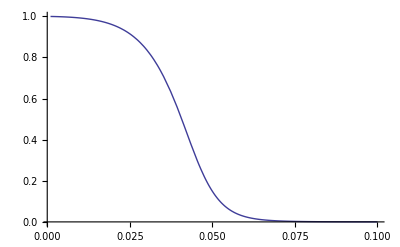

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.04001},
Plot[SABROptionAnalyticDistribution[f,α,β,ρ,ν,K,T],{K,0.001,0.1}]]
```

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.5,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581},
Plot[SABRHaganDistribution[f,α,β,ρ,ν,K,T],{K,0.001,0.1}]]
```

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,p=0.001,
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Tanh,0.05,1.5}}},
{SABROptionDistribution[f,α,β,ρ,ν,Meth1,p,T],SABROptionDistribution[f,α,β,ρ,ν,Meth2,p,T]}]
```

{0.00113512,0.000332846}

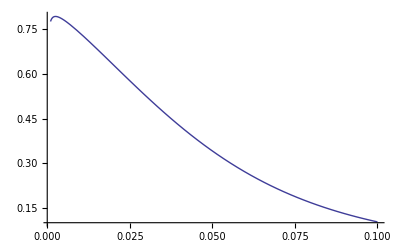

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.501,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581,
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Exponential,0.01}}},
Plot[1-SABROptionDistribution[f,α,β,ρ,ν,Meth1,K,T],{K,0.001,0.1}]]
```

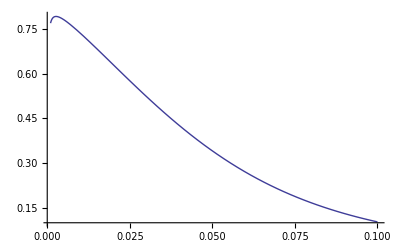

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.5,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581},
Plot[SABROptionAnalyticDistribution[f,α,β,ρ,ν,K,T],{K,0.001,0.1}]]
```

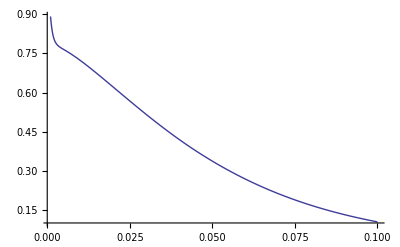

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.5,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581},
Plot[SABROptionAnalyticDistribution[f,α,β,ρ,ν,K,T],{K,0.001,0.1}]]
```

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.5,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581},
SABROptionAnalyticQuantile[f,α,β,ρ,ν,T,0.01]]
```

0.212396

```mathematica
Module[{f=0.043618130939813593,α=0.12004395604395604,T=3.0219178082191780,β=0.5,ATMvol,ρ=0.013026000000000001,ν=0.28653117582417581,p=0.9},
SABROptionAnalyticQuantile[f,α,β,ρ,ν,T,p]]
```

Max::nord: Invalid comparison with 0.0417284  + 0.0199426\ ⅈ attempted.

General::stop: Further output of Max :: "nord" will be suppressed during this calculation.

0.00187974-0.0199426 ⅈ

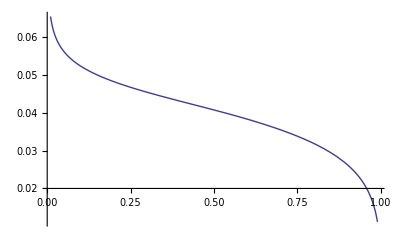

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.04001},
Plot[SABROptionAnalyticQuantile[f,α,β,ρ,ν,T,p],{p,0.01,0.99}]]
```

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.04001},
ATMvol=SABROptionAnalytic[f,α,β,ρ,ν,f,T,printflag][[1]];
Print["ATMvol=",ATMvol];
{ATMvol,SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,f,T]}]
```

ATMvol=0.115257562480890376303268873297

{0.115257562480890376303268873297,{0.115257868302004779213039320002,0.00410133}}

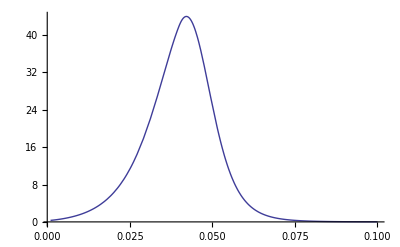

```mathematica
Module[{f=0.04,α=0.0435,T=5,β=0.7,ATMvol,ρ=-0.5,ν=0.3,K=0.04001},
Plot[SABROptionAnalyticDensity[f,α,β,ρ,ν,K,T],{K,0.001,0.1}]]
```

```mathematica
SABRDirect quick!
```

```mathematica
SABROptionDirect[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,fav,ξ,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
If[z==0,θ=1;sig=K^(-1+β) α(1-2 T(K^(2 β) α^2 (-1+β)^2+K^2 ν (6 b1 α ρ+ν (2-3 ρ^2)))/(24 K^2))^(-1/2),
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z];
sig=Log[f/K]/z ξ/(ν x)(1-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2))^(-1/2)];
result={sig,BS[f,K,T,sig ]};

result];
```

```mathematica
SABROptionDirect2[f_,α_,β_,ρ_,ν_,K_,T_]:=Module[{z,zp,x,b1,θ,ς,κ,result,σ,a,b,sig,sigN,fav2,γ1,γ2,ξ,fav,call},
fav=(f+K)/2;
If[β≠1, z=(f^(1-β)-K^(1-β))/(α (1-β)),z=Log[f]/α-Log[K]/α];
If[β≠1, ξ=ν(f^(1-β)-K^(1-β))/(α (1-β)), ξ=ν(Log[f]/α-Log[K]/α)];
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;
b1=β fav^(β-1);
θ=1/4 α b1 ν ρ z^2+Log[(α (f K)^(β/2) z)/(f-K)]+Log[(x (1-2 ν ρ z+ν^2 z^2)^(1/4))/z];
sig=Log[f/K]/z ξ/(ν x)(Exp[-2 T((θ-Log[(Log[f/K] √(f K))/(f-K)])/x^2)])^(-1/2);
result={sig,BS[f,K,T,sig ]};

result];
```

```mathematica
Module[{f=0.04,
α=0.0435,T1=50,T2=20,T3=50,β=0.7,ρ=-0.5,ν=0.3,K=0.04001},
{SABROptionDirect[f,α,β,ρ,ν,K,T1],SABROptionAnalytic[f,α,β,ρ,ν,K,T1],SABROptionDirect2[f,α,β,ρ,ν,K,T1]}]
```

{{0.125696,0.0137266},{0.125423025351977519184379009426,0.0136987},{0.12462,0.0136166}}

```mathematica
Module[{f=0.04,
α=0.0435,T1=50,T2=20,T3=50,β=0.7,ρ=-0.5,ν=0.3,K=0.04},
{SABROptionDirect[f,α,β,ρ,ν,K,T1],SABROptionAnalytic[f,α,β,ρ,ν,K,T1],SABROptionDirect[f,α,β,ρ,ν,K,T1]}]
```

{{0.125693,0.0137296},{0.12544793108796800693054221853,0.0137046},{0.125693,0.0137296}}

```mathematica
Generic Agorithms
```

```mathematica
SABRgeneric5[intrinsec_,z_,b1_,b2_,zavg_,SqB0Bαz_,T_,μ_,α_,ρ_,ν_,printflag_]:=
Module[{x,I0,I1,I2,κ,f1overf0,xp},
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;(*  x    est la distance geodesique , on approxime la prob de transition par ⅇ^(-x^2/(2T))(1+..)  *)
If[printflag>0,Print["SABRgeneric5:z=",SetPrecision[z,12]," zavg=",SetPrecision[zavg,12]," ρ=",SetPrecision[ρ,12]," ν=",SetPrecision[ν,12]," Iz2=",SetPrecision[1-2 ν ρ z+ν^2 z^2,12]," x=",SetPrecision[x,12]]];
If[printflag>20,
Plot[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ),{z1,-0.2,0.2},AxesLabel->{"z","x"}]];

I0=√(1+z ν (z ν-2 ρ));
I1=(z ν-ρ)/I0;
I2=(1-ρ^2)/I0^3;
κ=(12  μ+ (-3 b1^2 +2 b2) α^2-4 z^2 μ^2+((3 I0^2-1) I0 I2-I1^2) ν^2+(6 b1 α -16 z μ )ν ρ)/8;


f1overf0=ⅇ^((1/4 α b1 ν ρ+μ/2) z^2);
f1overf0=ⅇ^(((2 μ+b1 α  ν ρ) (2 ρ ArcTan[(z  ν-ρ)/(√(1-ρ^2))]+2 ρ ArcTan[ρ/(√(1-ρ^2))]+√(1-ρ^2) Log[1+z^2  ν^2-2 z  ν ρ]))/(4  ν^2 √(1-ρ^2)));

If[printflag>20,
Plot[ GIntegralAnalytical3[√-κ,Abs[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ)]/(√2),√T],{z1,-0.2,0.2},AxesLabel->{"z","GIntegralAnalytical3[x[z]]"},PlotRange->All]];

If[printflag>0,Print[" f1overf0=",SetPrecision[f1overf0,12]," SqB0Bαz=",SetPrecision[SqB0Bαz,12]," I0=",SetPrecision[I0,12]," κ=",SetPrecision[κ,12]," GIntegralAnalytical[√-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical[√-κ,Abs[x]/(√2),√T],12],
" GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical2[-κ,Abs[x]/(√2),√T],12]," intrinsec=",intrinsec]];
If[printflag>20,Plot[ GIntegralAnalytical3[√-κ,Abs[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ)]/(√2),√T],{z1,-0.2,0.2},AxesLabel->{"z","GIntegralAnalytical3[x[z]]"},PlotRange->All]];
intrinsec+α/2 √(2/π)SqB0Bαz  f1overf0 √I0 GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]]
```

```mathematica
SABRgeneric6[intrinsec_,z_,b1_,b2_,zavg_,SqB0Bαz_,T_,μ_,α_,ρ_,ν_,printflag_]:=
Module[{x,I0,I1,I2,κ,f1overf0,xp},
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;(*  x    est la distance geodesique , on approxime la prob de transition par ⅇ^(-x^2/(2T))(1+..)  *)
If[printflag>0,Print["SABRgeneric5:z=",SetPrecision[z,12]," zavg=",SetPrecision[zavg,12]," ρ=",SetPrecision[ρ,12]," ν=",SetPrecision[ν,12]," Iz2=",SetPrecision[1-2 ν ρ z+ν^2 z^2,12]," x=",SetPrecision[x,12]]];
If[printflag>20,
Plot[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ),{z1,-0.2,0.2},AxesLabel->{"z","x"}]];

I0=√(1+z ν (z ν-2 ρ));
I1=(z ν-ρ)/I0;
I2=(1-ρ^2)/I0^3;
(*κ=(12  μ+ (-3 b1^2 +2 b2) α^2-4 z^2 μ^2+(2 I0 I2-I1^2) ν^2+(6 b1 α -16 zavg μ )ν ρ)/(8 (1+zavg  ν (z  ν-2 ρ)));*)
κ=(12  μ+ (-3 b1^2 +2 b2) α^2-4 z^2 μ^2+((3 I0^2-1) I0 I2-I1^2) ν^2+(6 b1 α -16 z μ )ν ρ)/8;(* avec la modif qui stabilise et qui reprice hagan *)
f1overf0=ⅇ^((1/4 α b1 ν ρ+μ/2) z^2);

If[printflag>20,
Plot[ GIntegralAnalytical3[√-κ,Abs[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ)]/(√2),√T],{z1,-0.2,0.2},AxesLabel->{"z","GIntegralAnalytical3[x[z]]"},PlotRange->All]];

If[printflag>0,Print["SABRgeneric5: f1overf0=",SetPrecision[f1overf0,12]," SqB0Bαz=",SetPrecision[SqB0Bαz,12]," I0=",SetPrecision[I0,12]," κ=",SetPrecision[κ,12]," GIntegralAnalytical[√-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical[√-κ,Abs[x]/(√2),√T],12],
" GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical2[-κ,Abs[x]/(√2),√T],12]," intrinsec=",intrinsec]];
If[printflag>20,Plot[ GIntegralAnalytical3[√-κ,Abs[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ)]/(√2),√T],{z1,-0.2,0.2},AxesLabel->{"z","GIntegralAnalytical3[x[z]]"},PlotRange->All]];
intrinsec+1.1 α/2 √(2/π)SqB0Bαz  f1overf0 √I0 GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]]
```

```mathematica
SABRgeneric5[intrinsec_,z_,b1_,b2_,SqB0Bαz_,f_,K_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{x,d,I0,I1,I2,κ,f1overf0,xp,z1},
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;(*  x    est la distance geodesique , on approxime la prob de transition par ⅇ^(-x^2/(2T))DetVanVleck (1+..)  *)
If[printflag>0,
Plot[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ),{z1,-0.2,0.2},AxesLabel->{"z","x"}]];
f1overf0=ⅇ^((1/4 α b1 ν ρ+μ/2) z^2);

I0=√(1-2 ν ρ z+ν^2 z^2);
I1=(z ν-ρ)/I0;
I2=(1-ρ^2)/I0^3;

(*κ=(12  μ+ (-3 b1^2 α^2+2 b2 α^2-4 z^2 μ^2-I1^2 ν^2+2 I0 I2 ν^2+6 b1 α ν ρ-16 z μ ν ρ))/(8 I0^2);*)

κ=(12  μ+ (-3 b1^2 α^2+2 b2 α^2-4 z^2 μ^2-I1^2 ν^2+(3 I0^2-1) I0 I2 ν^2+6 b1 α ν ρ-16 z μ ν ρ))/8; (* avec la modif qui stabilise et qui reprice hagan *)



If[printflag>0,
Plot[ GIntegralAnalytical3[√-κ,Abs[(-ρ+ν z1+√(1-2 ν ρ z1+ν^2 z1^2))/(1-ρ)]/(√2),√T],{z1,-0.2,0.2},AxesLabel->{"z","GIntegralAnalytical3[x[z]]"},PlotRange->All]];
If[printflag>0,Print["SABRgeneric5:z=",z,",  x=",x]];

If[printflag>0,Print["SABRgeneric5: f1overf0=",f1overf0," SqB0Bαz=",SqB0Bαz," I0=",I0," κ=",κ," GIntegralAnalytical3[√-κ,Abs[x]/SqrtBox[2],√T]=",GIntegralAnalytical3[√-κ,Abs[x]/(√2),√T]]];
intrinsec+f1overf0/(√(2π))α  SqB0Bαz √I0 Re[GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]]]
```

```mathematica
SABRUsuelPlus5[f_,K_,T_,A_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b1,b2,B0Bαz,favg,zavg,intrinsec,I0,I1,I2,call,result},
z=((A+f)^(1-β) -(A+K)^(1-β))/(α  (1-β));
favg=(f+K)/2;
b1=β(favg+A)^(β-1);
b2=β(β-1)(favg+A)^(β-2)(favg+A)^β+b1^2;
B0Bαz=(A+K)^β(A+f)^β;
intrinsec=Max[f-K,0];
call=SABRgeneric5[intrinsec,z,b1,b2,√B0Bαz,f,K,T,0,α,ρ,ν,printflag];
If[printflag>0,Print["b1=",b1," b2=",b2," √B0Bαz=",√B0Bαz," z=",z," intrinsec=",intrinsec," favg=",favg," call=",call]];
result={ImpVolBS[f,K,T,1,call],call};
result
]
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=0.7,
ρ=-0.5,
ν=0.3798,
K=0.08,
T=4,printflag=0,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic"},
op=SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T];
Print["op=",op];
{SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,1]}]
```

op={0.120003840364764269896723597989,0.0000144042}

SABRgeneric5:z=-6.35578,  x=-5.48473

SABRgeneric5: f1overf0=0.873534 SqB0Bαz=0.135986 I0=2.10074 κ=0.0113436 GIntegralAnalytical3[√-κ,Abs[x]/SqrtBox[2],√T]=0.00480516+0. ⅈ

b1=1.62074 b2=1.50102 √B0Bαz=0.135986 z=-6.35578 intrinsec=0 favg=0.0609 call=0.0000143571

{{0.119963925520412611962842759918,0.0000143571}}

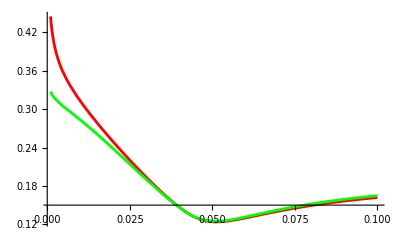
{-Graphics-,{0.168540597132506207054574598489,{0.16711346436709688270238808162,0.0206729}}}

```mathematica
Module[{f=0.0418,
α=0.0435,
β=0.7,
ρ=-0.5,
ν=0.3798,
K=0.035,
T=50,printflag=0,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic"},
{Plot[{SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,0][[1]],
SABROptionAnalytic[f,α,β,ρ,ν,K,T][[1]]},{K,0.001,0.1},PlotStyle->{{Thickness[0.005],RGBColor[1,0,0]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[0.5,0.2,0.5]}},PlotLegend->{"SABRUsuelPlus5","SABR Type Analytic"},LegendPosition->{-2,0.}],
{SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,0][[1]],SABROptionAnalytic[f,α,β,ρ,ν,K,T]}}]
```

```mathematica
(* Distance geodesique exacte pour verifier x   *)
```

```mathematica
Plot3D[Log[(-ρ+νz+√(1-2 ρ νz+ νz^2))/(1-ρ)] , {νz,-5,5},{ρ,0,0.99}]
```

-Graphics3D-

```mathematica
On projete le distance geodesique sur l'hyperplan S=cste,σ quelconque
```

```mathematica
Clear[δ]
```

```mathematica
δ[x_,y_,X_,Y_]:=ArcCosh[1+((∫_X^x 1/C[s] ⅆs)^2-2ρ(y-Y)∫_X^x 1/C[s] ⅆs+(y-Y)^2)/(2(1-ρ^2)y Y)]
```

```mathematica
Simplify[Simplify[δ[x,y,X,Y] /. rules[[2]],y>0 && Y>0 && ρ^2<1] /. {∫_X^x 1/C[s] ⅆs->z}]
```

ArcCosh[(-y^2-z (z+ρ √(y^2+z^2-2 y z ρ))+y ρ (2 z+ρ √(y^2+z^2-2 y z ρ)))/(y √(y^2+z^2-2 y z ρ) (-1+ρ^2))]

```mathematica
δ[z_,y_,Y_]:=ArcCosh[1+(z^2-2ρ(y-Y)z+(y-Y)^2)/(2(1-ρ^2)y Y)]
```

```mathematica
Simplify[D[δ[ν z,y,Y],Y],y>0 && Y>0 && ρ^2<1]
```

(-y^2+Y^2-z^2 ν^2+2 y z ν ρ)/(Y √(y^2+Y^2+z^2 ν^2+2 Y z ν ρ-2 y (Y+z ν ρ)) √(y^2+Y^2+z^2 ν^2+2 Y z ν ρ-2 y (z ν ρ+Y (-1+2 ρ^2))))

```mathematica
Solve[-y^2+Y^2-z^2 ν^2+2 y z ν ρ==0,Y]
```

{{Y→-√(y^2+z^2 ν^2-2 y z ν ρ)},{Y→√(y^2+z^2 ν^2-2 y z ν ρ)}}

```mathematica
Simplify[δ[ν z,y,Y]/.{Y->√(y^2+z^2 ν^2-2 y z ν ρ)}] /.{ y->α}
```

ArcCosh[(-α^2-z ν (z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ))+α ρ (2 z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ)))/(α √(α^2+z^2 ν^2-2 z α ν ρ) (-1+ρ^2))]

```mathematica
Solve[(X+1/X)/2==y,X]
```

{{X→y-√(-1+y^2)},{X→y+√(-1+y^2)}}

```mathematica
Simplify[Log[m+√(-1+m^2)]/. {m->(-α^2-z ν (z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ))+α ρ (2 z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ)))/(α √(α^2+z^2 ν^2-2 z α ν ρ) (-1+ρ^2))}]
```

Log[√((z^2 ν^2 (1+ρ^2)+2 α ρ^2 (α-√(α^2+z^2 ν^2-2 z α ν ρ))-2 z ν ρ (α+α ρ^2-√(α^2+z^2 ν^2-2 z α ν ρ)))/(α^2 (-1+ρ^2)^2))+(-α^2-z ν (z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ))+α ρ (2 z ν+ρ √(α^2+z^2 ν^2-2 z α ν ρ)))/(α √(α^2+z^2 ν^2-2 z α ν ρ) (-1+ρ^2))]

```mathematica
C'est la meme formule que lesnieski
```

```mathematica
Module[{ρ=0.7,ν=0.2,z=1},{(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ),√((z^2 ν^2 (1+ρ^2)-2 z ν ρ (1+ρ^2-√(1+z^2 ν^2-2 z ν ρ))-2 ρ^2 (-1+√(1+z^2 ν^2-2 z ν ρ)))/((-1+ρ^2)^2))+(-1-z ν (z ν+ρ √(1+z^2 ν^2-2 z ν ρ))+ρ (2 z ν+ρ √(1+z^2 ν^2-2 z ν ρ)))/(√(1+z^2 ν^2-2 z ν ρ) (-1+ρ^2))}]
```

{1.23927,1.23927}

```mathematica
Simplify[Expand[((z ν - ρ)+ ρ √(1+z^2 ν^2-2 z ν ρ))^2]-(z^2 ν^2 (1+ρ^2)-2 z ν ρ (1+ρ^2-√(1+z^2 ν^2-2 z ν ρ))-2 ρ^2 (-1+√(1+z^2 ν^2-2 z ν ρ)))]
```

0

```mathematica
Simplify[-1-z ν (z ν+ρ √(1+z^2 ν^2-2 z ν ρ))+ρ (2 z ν+ρ √(1+z^2 ν^2-2 z ν ρ)) - √(1+z^2 ν^2-2 z ν ρ)(ρ^2-ρ ν z -√(1+z^2 ν^2-2 z ν ρ))]
```

0

```mathematica
SABRgeneric7[intrinsec_,z_,b1_,b2_,SqB0Bαz_,f_,K_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{x,d,I0,I1,I2,κ,f1overf0,xp},
(*  x    est la distance geodesique , on approxime la prob de transition par ⅇ^(-x^2/(2T))(1+..)  *)
x=1/ν ArcCosh[(-1-z ν (z ν+ρ √(1+z^2 ν^2-2 z  ν ρ))+ ρ (2 z ν+ρ √(1+z^2 ν^2-2 z  ν ρ)))/(√(1+z^2 ν^2-2 z  ν ρ) (-1+ρ^2))];
f1overf0=ⅇ^((1/4 α b1 ν ρ+μ/2) z^2);

I0=√(1-2 ν ρ z+ν^2 z^2);
I1=(z ν-ρ)/I0;
I2=(1-ρ^2)/I0^3;

(* original  : κ=(12  μ+ (-3 b1^2 α^2+2 b2 α^2-4 z^2 μ^2-I1^2 ν^2+2 I0 I2 ν^2+6 b1 α ν ρ-16 z μ ν ρ))/(8 I0^2); *)

κ=(12  μ+ (-3 b1^2 +2 b2) α^2-4 z^2 μ^2+((3 I0^2-1) I0 I2-I1^2) ν^2+(6 b1 α -16 z μ )ν ρ)/8;(* avec la modif qui stabilise et qui reprice hagan *)
If[printflag>0,Print["SABRgeneric7:z=",z,",  x=",x," xp=",xp]];

If[printflag>0,Print["SABRgeneric7: f1overf0=",f1overf0," SqB0Bαz=",SqB0Bαz," I0=",I0," κ=",κ," GIntegralAnalytical3[√-κ,Abs[x]/SqrtBox[2],√T]=",GIntegralAnalytical3[√-κ,Abs[x]/(√2),√T]]];
intrinsec+f1overf0/(√(2π))α  SqB0Bαz √I0 Re[GIntegralAnalytical3[√-κ,Abs[x]/(√2),√T]]]
```

```mathematica
SABRUsuelPlus7[f_,K_,T_,A_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b1,b2,B0Bαz,favg,zavg,intrinsec,I0,I1,I2,call,result},
z=((A+f)^(1-β) -(A+K)^(1-β))/(α  (1-β));
favg=(f+K)/2;
b1=β(favg+A)^(β-1);
b2=β(β-1)(favg+A)^(β-2)(favg+A)^β+b1^2;
B0Bαz=(A+K)^β(A+f)^β;
intrinsec=Max[f-K,0];
call=SABRgeneric7[intrinsec,z,b1,b2,√B0Bαz,f,K,T,0,α,ρ,ν,printflag];
If[printflag>0,Print["b1=",b1," b2=",b2," √B0Bαz=",√B0Bαz," z=",z," intrinsec=",intrinsec," favg=",favg," call=",call]];
result={ImpVolBS[f,K,T,1,call],call};
result
]
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1.7,
ρ=-0.5,
ν=10.3798,
K=0.035,
T=4,printflag=0,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic"},
{SABRUsuelPlus7[f,K,T,0,α,β,ρ,ν,0][[1]],
SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,0][[1]]}]
```

{0.0396768911506204851919759133822,0.0464130053988405844197915762687}

```mathematica
Module[{f=0.0418,
α=0.0435,
β=0.7,
ρ=-0.5,
ν=0.3798,
K=0.08,
T=20,printflag=0,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic"},
Plot[{SABRUsuelPlus7[f,K,T,0,α,β,ρ,ν,0][[1]]-
SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,0][[1]]},{K,0.001,0.1}]]
```

⁃Graphics⁃

```mathematica
Proof
```

```mathematica
Clear[x,I0,z,b0,b1,b2,b3,b4,f,K,s,ν,ρ,favg,zavg]
```

```mathematica
(*         ∫_K^f 1/C[s] ⅆs->ϵ α z,C[f]->B[ϵ α z]           *)
```

```mathematica
rr={∫_favg[f]^u_ 1/C[s] ⅆs->α(z[f]-zavg)};
```

```mathematica
favg[f_]:=(f+K)/2
```

```mathematica
z[f_]:=1/α∫_K^f 1/C[s] ⅆs;(* zavg:=1/α∫_K^favg 1/C[s] ⅆs,     favg[f_]:=(f+K)/2 *)
```

```mathematica
(*              theta[f_]:=Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K)]+1/4 ρ ν α C'[K] z[favg[f]]^2     *)
```

```mathematica
I0[z_]:=√(1-2 ν ρ z+ν^2 z^2)
```

```mathematica
x[z_]:=Log[(-ρ+ν z+I0[z])/(1-ρ)]/ν
```

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((1/4 ρ ν α C'[favg[f]]  C[K] z[f]^2+Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ])T)/x[z[f]]^2),{f,K,1}]],C[K]>0]/. {C[K]->b0,C'[K]-> b1,C''[K]->(b2-b1^2)/b0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

1/48 (48 b0 α-24 b1 (-f+K) α+24 (-f+K) ν ρ)+1/48 T (-6 b0 b1^2 α^3+3 b1^3 (-f+K) α^3-2 b1 b2 (-f+K) α^3+4 b0 α ν^2+12 b0^2 b1 α^2 ν ρ-9 b1^2 (-f+K) α^2 ν ρ+6 b2 (-f+K) α^2 ν ρ-6 b0 α ν^2 ρ^2+18 b0 b1 (-f+K) α ν^2 ρ^2+2 b0 b2 α^2 (2 α+3 (f-K) ν ρ)-b1 (-f+K) α ν^2 (2-3 ρ^2)+(-f+K) ν^3 ρ (-4+3 ρ^2))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((1/4 ρ ν α C'[favg[f]]  C[K] z[f]^2)T)/x[z[f]]^2),{f,K,1}]],C[K]>0]/. {∫_((f+K)/2)^u_ 1/C[s] ⅆs->α(z[u]-zavg),C[K]->b0,C'[K]-> b1,C''[K]->(b2-b1^2)/b0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

1/8 T (2 b0^2 b1 α^2 ν ρ+b0 b2 (f-K) α^2 ν ρ+3 b0 b1 (-f+K) α ν^2 ρ^2)+1/8 (8 b0 α+4 (f-K) (b1 α-ν ρ))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](((Log[α  √(C[K] C[f]) x[z[f]]/(f-K) ])T)/x[z[f]]^2),{f,K,0}]],C[K]>0]/. {C[K]->b0,C'[K]-> b1,C''[K]->(b2-b1^2)/b0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

-(b0 T α (-2 b0 α (((-b1^2+b2) (f-K) α)/b0+6 ν ρ)+(f-K) (b1^2 α^2-12 b1 α ν ρ+ν^2 (4+9 ρ^2))))/(24 (f-K))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](((Log[√I0[z[f]]])T)/x[z[f]]^2),{f,K,0}]],C[K]>0]/. {C[K]->b0,C'[K]-> b1,C''[K]->(b2-b1^2)/b0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

(b0 T α ν (-2 b0 α ρ+(f-K) (ν-2 b1 α ρ+ν ρ^2)))/(4 (f-K))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ])T)/x[z[f]]^2),{f,K,1}]],C[K]>0]/. {C[K]->b0,C'[K]-> b1,C''[K]->(b2-b1^2)/b0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

-1/48 T (b0 (6 b1^2 α^3-4 b2 α^3+2 α ν^2 (-2+3 ρ^2))+(f-K) (3 b1^3 α^3-9 b1^2 α^2 ν ρ+ν ρ (6 b2 α^2+ν^2 (-4+3 ρ^2))+b1 (-2 b2 α^3+α ν^2 (-2+3 ρ^2))))

```mathematica
Simplify[Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((1/4 ρ ν α C'[favg[f]]  C[K] z[f]^2+Log[α x[z[f]]/(f-K) √(C[K] C[f] I0[z[f]])])T)/x[z[f]]^2),{K,f,0}]],C[K]>0]/. {C[f]->bz,C'[f]-> b1,C''[f]->(b2-b1^2)/bz,Derivative[3][C][f]->0,Derivative[4][C][f]->0}],T],bz>0 ]
```

bz α+1/24 bz T α (-3 b1^2 α^2+2 b2 α^2+6 b1 bz α ν ρ+ν^2 (2-3 ρ^2))

```mathematica
Simplify[Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]],{K,f,0}]],C[K]>0]/. {C[f]->bz,C'[f]-> b1,C''[f]->(b2-b1^2)/bz,Derivative[3][C][f]->0,Derivative[4][C][f]->0}],T],bz>0 ]
```

bz α

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2),{f,K,2}]],C[K]>0]/. {C[K]->b0,C'[K]->b0 b1,C''[K]->0,Derivative[3][C][K]->0,Derivative[4][C][K]->0}],T]
```

-(-2880 b0^2 α^2-1440 b0^2 b1 (f-K) α^2+240 b0^2 b1^2 (f-K)^2 α^2+1440 b0 (f-K) α ν ρ+240 (f-K)^2 ν^2 (-2+3 ρ^2))/(2880 b0 α)-1/(2880 b0 α)(T (120 b0^4 b1^2 α^4+60 b0^4 b1^3 (f-K) α^4-11 b0^4 b1^4 (f-K)^2 α^4-720 b0^3 b1 α^3 ν ρ-540 b0^3 b1^2 (f-K) α^3 ν ρ+60 b0^3 b1^3 (f-K)^2 α^3 ν ρ-360 b0 b1 (f-K)^2 α ν^3 ρ+10 b0^2 b1^2 (f-K)^2 α^2 ν^2 (8-3 ρ^2)+60 b0 (f-K) α ν^3 ρ (-4+3 ρ^2)+120 b0^2 α^2 ν^2 (-2+3 ρ^2)+60 b0^2 b1 (f-K) α^2 ν^2 (-2+21 ρ^2)+(f-K)^2 ν^4 (64-300 ρ^2+225 ρ^4)))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2),{f,K,4}]],C[K]>0]/. {C[K]->b0,C'[K]->b0 b1,C''[K]->b0 b2,Derivative[3][C][K]->b0 b3,Derivative[4][C][K]->b0 b4,Derivative[5][C][K]->0,Derivative[6][C][K]->0}],T]
```

-1/(362880 b0^3 α^3)(-362880 b0^4 α^4-181440 b0^4 b1 (f-K) α^4+30240 b0^4 b1^2 (f-K)^2 α^4-60480 b0^4 b2 (f-K)^2 α^4-15120 b0^4 b1^3 (f-K)^3 α^4+30240 b0^4 b1 b2 (f-K)^3 α^4-15120 b0^4 b3 (f-K)^3 α^4+9576 b0^4 b1^4 (f-K)^4 α^4-23184 b0^4 b1^2 b2 (f-K)^4 α^4+8064 b0^4 b2^2 (f-K)^4 α^4+9072 b0^4 b1 b3 (f-K)^4 α^4-3024 b0^4 b4 (f-K)^4 α^4+181440 b0^3 (f-K) α^3 ν ρ-10080 b0^2 b1^2 (f-K)^4 α^2 ν^2 (2-3 ρ^2)+30240 b0^2 (f-K)^2 α^2 ν^2 (-2+3 ρ^2)-15120 b0^2 b1 (f-K)^3 α^2 ν^2 (-2+3 ρ^2)-5040 b0^2 b2 (f-K)^4 α^2 ν^2 (-2+3 ρ^2)+15120 b0 (f-K)^3 α ν^3 ρ (-5+6 ρ^2)-15120 b0 b1 (f-K)^4 α ν^3 ρ (-5+6 ρ^2)+504 (f-K)^4 ν^4 (34-240 ρ^2+225 ρ^4))-1/(362880 b0^3 α^3)(T (-1512 b0^6 (20 b2+(10 b3+3 b4 (f-K)) (f-K)) α^6+9 b0^6 (1680 b1^2-28 b1 (60 b2+(36 b3+11 b4 (f-K)) (f-K)) (f-K)-(616 b2^2+20 b2 (21 b3+5 b4 (f-K)) (f-K)+55 b3^2 (f-K)^2) (f-K)^2) α^6+7560 b0^6 b1^3 (f-K) α^6-1386 b0^6 b1^4 (f-K)^2 α^6+693 b0^6 b1^5 (f-K)^3 α^6+2772 b0^6 b1 b2^2 (f-K)^3 α^6-439 b0^6 b1^6 (f-K)^4 α^6-2496 b0^6 b1^2 b2^2 (f-K)^4 α^6+740 b0^6 b2^3 (f-K)^4 α^6+756 b0^5 b2^2 (f-K)^3 α^5 ν ρ+378 b0^5 b1^2 (18 b2+5 b3 (f-K)) (f-K)^3 α^5 ν ρ+2205 b0^5 b1^5 (f-K)^4 α^5 ν ρ+1260 b0^5 b1 b2^2 (f-K)^4 α^5 ν ρ-2268 b0^5 (40 b1-(f-K) (20 b2+(f-K) (10 b3+3 b4 f-3 b4 K))) α^5 ν ρ-45360 b0^3 b1 (f-K)^2 α^3 ν^3 ρ+18 b0^5 b1^2 (f-K) α^5 (b0 (308 b2+(77 b3+17 b4 (f-K)) (f-K)) (f-K) α-3780 ν ρ)+3 b0^5 b1^4 (f-K)^3 α^5 (647 b0 b2 (f-K) α-1197 ν ρ)-18 b0^5 b1^3 (f-K)^2 α^5 (b0 (154 b2+51 b3 (f-K)) (f-K) α-420 ν ρ)+180 b0^5 b1 b2 (f-K)^2 α^5 (11 b0 b3 (f-K)^2 α-84 ν ρ)-1890 b0^3 b1^2 (f-K)^3 α^3 ν^3 ρ (-13+ρ^2)+1890 b0^3 b1^3 (f-K)^4 α^3 ν^3 ρ (-9+ρ^2)+3780 b0^3 b2 (f-K)^3 α^3 ν^3 ρ (-1+ρ^2)+1890 b0^3 b3 (f-K)^4 α^3 ν^3 ρ (-1+ρ^2)+126 b0^4 b4 (f-K)^4 α^4 ν^2 (-20+3 ρ^2)+630 b0^4 b3 (f-K)^3 α^4 ν^2 (-14+3 ρ^2)-378 b0^4 b1 b3 (f-K)^4 α^4 ν^2 (-10+3 ρ^2)-1260 b0^4 b1^2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)+2520 b0^4 b2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)-1260 b0^4 b1 b2 (f-K)^3 α^4 ν^2 (-8+3 ρ^2)+7560 b0^3 (f-K) α^3 ν^3 ρ (-4+3 ρ^2)+15120 b0^4 α^4 ν^2 (-2+3 ρ^2)+105 b0^2 b2 (f-K)^4 α^2 ν^4 (-2+3 ρ^2)^2-84 b0^4 b2^2 (f-K)^4 α^4 ν^2 (-35+12 ρ^2)-21 b0^4 b1^4 (f-K)^4 α^4 ν^2 (-155+57 ρ^2)+42 b0^4 b1^2 b2 (f-K)^4 α^4 ν^2 (-190+69 ρ^2)-315 b0 b1 (f-K)^4 α ν^5 ρ (56-138 ρ^2+81 ρ^4)+126 b0^2 (f-K)^2 α^2 ν^4 (64-300 ρ^2+225 ρ^4)-21 b0^2 b1^2 (f-K)^4 α^2 ν^4 (-86-120 ρ^2+225 ρ^4)+63 b0 (f-K)^3 α ν^5 ρ (364-1050 ρ^2+675 ρ^4)+(f-K)^4 ν^6 (-4660+59031 ρ^2-123795 ρ^4+68985 ρ^6)-630 b0^4 b1^3 (f-K)^3 α^4 ν (8 b0 b2 (f-K) α ρ+ν (8-3 ρ^2))-1512 b0^4 b1 (f-K) α^4 ν (b0 b3 (f-K)^2 α ρ-5 ν (-2+21 ρ^2))-63 b0^2 b1 (f-K)^3 α^2 ν^3 (60 b0 b2 (f-K) α ρ (-3+ρ^2)+ν (64-120 ρ^2+45 ρ^4))))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]](1+((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2),{f,K,4}]],C[K]>0]/. {C[K]->b0,C'[K]->b0 b1,C''[K]->b0 b2,Derivative[3][C][K]->0,Derivative[4][C][K]->0,Derivative[5][C][K]->0,Derivative[6][C][K]->0}],T]
```

-1/(362880 b0^3 α^3)(-362880 b0^4 α^4-181440 b0^4 b1 (f-K) α^4+30240 b0^4 b1^2 (f-K)^2 α^4-60480 b0^4 b2 (f-K)^2 α^4-15120 b0^4 b1^3 (f-K)^3 α^4+30240 b0^4 b1 b2 (f-K)^3 α^4+9576 b0^4 b1^4 (f-K)^4 α^4-23184 b0^4 b1^2 b2 (f-K)^4 α^4+8064 b0^4 b2^2 (f-K)^4 α^4+181440 b0^3 (f-K) α^3 ν ρ-10080 b0^2 b1^2 (f-K)^4 α^2 ν^2 (2-3 ρ^2)+30240 b0^2 (f-K)^2 α^2 ν^2 (-2+3 ρ^2)-15120 b0^2 b1 (f-K)^3 α^2 ν^2 (-2+3 ρ^2)-5040 b0^2 b2 (f-K)^4 α^2 ν^2 (-2+3 ρ^2)+15120 b0 (f-K)^3 α ν^3 ρ (-5+6 ρ^2)-15120 b0 b1 (f-K)^4 α ν^3 ρ (-5+6 ρ^2)+504 (f-K)^4 ν^4 (34-240 ρ^2+225 ρ^4))-1/(362880 b0^3 α^3)(T (-30240 b0^6 b2 α^6+504 b0^6 (30 b1^2-30 b1 b2 (f-K)-11 b2^2 (f-K)^2) α^6+7560 b0^6 b1^3 (f-K) α^6-1386 b0^6 b1^4 (f-K)^2 α^6+693 b0^6 b1^5 (f-K)^3 α^6+2772 b0^6 b1 b2^2 (f-K)^3 α^6-439 b0^6 b1^6 (f-K)^4 α^6-2496 b0^6 b1^2 b2^2 (f-K)^4 α^6+740 b0^6 b2^3 (f-K)^4 α^6-15120 b0^5 b1 b2 (f-K)^2 α^5 ν ρ+6804 b0^5 b1^2 b2 (f-K)^3 α^5 ν ρ+756 b0^5 b2^2 (f-K)^3 α^5 ν ρ+2205 b0^5 b1^5 (f-K)^4 α^5 ν ρ+1260 b0^5 b1 b2^2 (f-K)^4 α^5 ν ρ-45360 b0^5 (2 b1+b2 (-f+K)) α^5 ν ρ-45360 b0^3 b1 (f-K)^2 α^3 ν^3 ρ+18 b0^5 b1^2 (f-K) α^5 (308 b0 b2 (f-K) α-3780 ν ρ)+3 b0^5 b1^4 (f-K)^3 α^5 (647 b0 b2 (f-K) α-1197 ν ρ)-18 b0^5 b1^3 (f-K)^2 α^5 (154 b0 b2 (f-K) α-420 ν ρ)+1260 b0^4 b1^2 (f-K)^2 α^4 ν^2 (8-3 ρ^2)-1890 b0^3 b1^2 (f-K)^3 α^3 ν^3 ρ (-13+ρ^2)+1890 b0^3 b1^3 (f-K)^4 α^3 ν^3 ρ (-9+ρ^2)+3780 b0^3 b2 (f-K)^3 α^3 ν^3 ρ (-1+ρ^2)+2520 b0^4 b2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)-1260 b0^4 b1 b2 (f-K)^3 α^4 ν^2 (-8+3 ρ^2)+7560 b0^3 (f-K) α^3 ν^3 ρ (-4+3 ρ^2)+15120 b0^4 α^4 ν^2 (-2+3 ρ^2)+105 b0^2 b2 (f-K)^4 α^2 ν^4 (-2+3 ρ^2)^2-84 b0^4 b2^2 (f-K)^4 α^4 ν^2 (-35+12 ρ^2)+7560 b0^4 b1 (f-K) α^4 ν^2 (-2+21 ρ^2)-21 b0^4 b1^4 (f-K)^4 α^4 ν^2 (-155+57 ρ^2)+42 b0^4 b1^2 b2 (f-K)^4 α^4 ν^2 (-190+69 ρ^2)-315 b0 b1 (f-K)^4 α ν^5 ρ (56-138 ρ^2+81 ρ^4)+126 b0^2 (f-K)^2 α^2 ν^4 (64-300 ρ^2+225 ρ^4)-21 b0^2 b1^2 (f-K)^4 α^2 ν^4 (-86-120 ρ^2+225 ρ^4)+63 b0 (f-K)^3 α ν^5 ρ (364-1050 ρ^2+675 ρ^4)+(f-K)^4 ν^6 (-4660+59031 ρ^2-123795 ρ^4+68985 ρ^6)-630 b0^4 b1^3 (f-K)^3 α^4 ν (8 b0 b2 (f-K) α ρ+ν (8-3 ρ^2))-63 b0^2 b1 (f-K)^3 α^2 ν^3 (60 b0 b2 (f-K) α ρ (-3+ρ^2)+ν (64-120 ρ^2+45 ρ^4))))

```mathematica
(f-K)/x[z[f]](1+((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2) /.  {C[K]->b0,C'[K]->b0 b1,C''[K]->b0 b2,Derivative[3][C][K]->b0 b3,∫_K^f 1/C[s] ⅆs->α z,C[f]->bz}
```

((f-K) ν (1+(T ν^2 (1/4 b0 b1 z^2 α ν ρ+Log[(√(b0 bz) α (1+z^2 ν^2-2 z ν ρ)^(1/4) Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)])/((f-K) ν)]))/(Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)]^2)))/Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)]

```mathematica
Generic Function
```

```mathematica
SABRgenericNormalVol[f_,K_,z_,b0_,b1_,b2_,b3_,b4_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{x,σN,Q,ratio},
If[printflag>0, Print["SABRgenericNormalVol:K=",K," z=",z," b0=",b0," b1=",b1," b2=",b2," b3=",b3," b4=",b4," bz=",bz," μ=",μ," α=",α," ρ=",ρ," ν=",ν]];
If[Abs[f-K]<f/5,
(* development a la monnaie *)
σN=-1/(362880 b0^3 α^3)(-362880 b0^4 α^4-181440 b0^4 b1 (f-K) α^4+30240 b0^4 b1^2 (f-K)^2 α^4-60480 b0^4 b2 (f-K)^2 α^4-15120 b0^4 b1^3 (f-K)^3 α^4+30240 b0^4 b1 b2 (f-K)^3 α^4-15120 b0^4 b3 (f-K)^3 α^4+9576 b0^4 b1^4 (f-K)^4 α^4-23184 b0^4 b1^2 b2 (f-K)^4 α^4+8064 b0^4 b2^2 (f-K)^4 α^4+9072 b0^4 b1 b3 (f-K)^4 α^4-3024 b0^4 b4 (f-K)^4 α^4+181440 b0^3 (f-K) α^3 ν ρ-10080 b0^2 b1^2 (f-K)^4 α^2 ν^2 (2-3 ρ^2)+30240 b0^2 (f-K)^2 α^2 ν^2 (-2+3 ρ^2)-15120 b0^2 b1 (f-K)^3 α^2 ν^2 (-2+3 ρ^2)-5040 b0^2 b2 (f-K)^4 α^2 ν^2 (-2+3 ρ^2)+15120 b0 (f-K)^3 α ν^3 ρ (-5+6 ρ^2)-15120 b0 b1 (f-K)^4 α ν^3 ρ (-5+6 ρ^2)+504 (f-K)^4 ν^4 (34-240 ρ^2+225 ρ^4))-1/(362880 b0^3 α^3)(T (-1512 b0^6 (20 b2+(10 b3+3 b4 (f-K)) (f-K)) α^6+9 b0^6 (1680 b1^2-28 b1 (60 b2+(36 b3+11 b4 (f-K)) (f-K)) (f-K)-(616 b2^2+20 b2 (21 b3+5 b4 (f-K)) (f-K)+55 b3^2 (f-K)^2) (f-K)^2) α^6+7560 b0^6 b1^3 (f-K) α^6-1386 b0^6 b1^4 (f-K)^2 α^6+693 b0^6 b1^5 (f-K)^3 α^6+2772 b0^6 b1 b2^2 (f-K)^3 α^6-439 b0^6 b1^6 (f-K)^4 α^6-2496 b0^6 b1^2 b2^2 (f-K)^4 α^6+740 b0^6 b2^3 (f-K)^4 α^6+756 b0^5 b2^2 (f-K)^3 α^5 ν ρ+378 b0^5 b1^2 (18 b2+5 b3 (f-K)) (f-K)^3 α^5 ν ρ+2205 b0^5 b1^5 (f-K)^4 α^5 ν ρ+1260 b0^5 b1 b2^2 (f-K)^4 α^5 ν ρ-2268 b0^5 (40 b1-(f-K) (20 b2+(f-K) (10 b3+3 b4 f-3 b4 K))) α^5 ν ρ-45360 b0^3 b1 (f-K)^2 α^3 ν^3 ρ+18 b0^5 b1^2 (f-K) α^5 (b0 (308 b2+(77 b3+17 b4 (f-K)) (f-K)) (f-K) α-3780 ν ρ)+3 b0^5 b1^4 (f-K)^3 α^5 (647 b0 b2 (f-K) α-1197 ν ρ)-18 b0^5 b1^3 (f-K)^2 α^5 (b0 (154 b2+51 b3 (f-K)) (f-K) α-420 ν ρ)+180 b0^5 b1 b2 (f-K)^2 α^5 (11 b0 b3 (f-K)^2 α-84 ν ρ)-1890 b0^3 b1^2 (f-K)^3 α^3 ν^3 ρ (-13+ρ^2)+1890 b0^3 b1^3 (f-K)^4 α^3 ν^3 ρ (-9+ρ^2)+3780 b0^3 b2 (f-K)^3 α^3 ν^3 ρ (-1+ρ^2)+1890 b0^3 b3 (f-K)^4 α^3 ν^3 ρ (-1+ρ^2)+126 b0^4 b4 (f-K)^4 α^4 ν^2 (-20+3 ρ^2)+630 b0^4 b3 (f-K)^3 α^4 ν^2 (-14+3 ρ^2)-378 b0^4 b1 b3 (f-K)^4 α^4 ν^2 (-10+3 ρ^2)-1260 b0^4 b1^2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)+2520 b0^4 b2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)-1260 b0^4 b1 b2 (f-K)^3 α^4 ν^2 (-8+3 ρ^2)+7560 b0^3 (f-K) α^3 ν^3 ρ (-4+3 ρ^2)+15120 b0^4 α^4 ν^2 (-2+3 ρ^2)+105 b0^2 b2 (f-K)^4 α^2 ν^4 (-2+3 ρ^2)^2-84 b0^4 b2^2 (f-K)^4 α^4 ν^2 (-35+12 ρ^2)-21 b0^4 b1^4 (f-K)^4 α^4 ν^2 (-155+57 ρ^2)+42 b0^4 b1^2 b2 (f-K)^4 α^4 ν^2 (-190+69 ρ^2)-315 b0 b1 (f-K)^4 α ν^5 ρ (56-138 ρ^2+81 ρ^4)+126 b0^2 (f-K)^2 α^2 ν^4 (64-300 ρ^2+225 ρ^4)-21 b0^2 b1^2 (f-K)^4 α^2 ν^4 (-86-120 ρ^2+225 ρ^4)+63 b0 (f-K)^3 α ν^5 ρ (364-1050 ρ^2+675 ρ^4)+(f-K)^4 ν^6 (-4660+59031 ρ^2-123795 ρ^4+68985 ρ^6)-630 b0^4 b1^3 (f-K)^3 α^4 ν (8 b0 b2 (f-K) α ρ+ν (8-3 ρ^2))-1512 b0^4 b1 (f-K) α^4 ν (b0 b3 (f-K)^2 α ρ-5 ν (-2+21 ρ^2))-63 b0^2 b1 (f-K)^3 α^2 ν^3 (60 b0 b2 (f-K) α ρ (-3+ρ^2)+ν (64-120 ρ^2+45 ρ^4)))),
(* cas normal *)
Q=√(1+z^2 ν^2-2 z ν ρ);

x=1/ν Log[(z ν-ρ+Q)/(1-ρ)];
ratio=x/(f-K);
If[printflag>0,Print["SABRgenericNormalVol:Q=",Q," x/(f-K)=",ratio," coef en T =",(1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]])/x^2 ]];

σN=Abs[ ((f-K)  (1+(T  (1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]]))/x^2))/x]]]
```

```mathematica
SABRgenericNormalVol[f_,K_,z_,b0_,b1_,b2_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{x,σN,Q,ratio},
 If[printflag>0,Print["SABRgenericNormalVol:K=",K," z=",z," b0=",b0," b1=",b1," b2=",b2," bz=",bz," μ=",μ," α=",α," ρ=",ρ," ν=",ν]];
If[Abs[f-K]<Max[0.05f,0.005],If[printflag>0,Print["++++DL"]];
(* development a la monnaie *)
σN=-1/(362880 b0^3 α^3)(-362880 b0^4 α^4-181440 b0^4 b1 (f-K) α^4+30240 b0^4 b1^2 (f-K)^2 α^4-60480 b0^4 b2 (f-K)^2 α^4-15120 b0^4 b1^3 (f-K)^3 α^4+30240 b0^4 b1 b2 (f-K)^3 α^4+9576 b0^4 b1^4 (f-K)^4 α^4-23184 b0^4 b1^2 b2 (f-K)^4 α^4+8064 b0^4 b2^2 (f-K)^4 α^4+181440 b0^3 (f-K) α^3 ν ρ-10080 b0^2 b1^2 (f-K)^4 α^2 ν^2 (2-3 ρ^2)+30240 b0^2 (f-K)^2 α^2 ν^2 (-2+3 ρ^2)-15120 b0^2 b1 (f-K)^3 α^2 ν^2 (-2+3 ρ^2)-5040 b0^2 b2 (f-K)^4 α^2 ν^2 (-2+3 ρ^2)+15120 b0 (f-K)^3 α ν^3 ρ (-5+6 ρ^2)-15120 b0 b1 (f-K)^4 α ν^3 ρ (-5+6 ρ^2)+504 (f-K)^4 ν^4 (34-240 ρ^2+225 ρ^4))-1/(362880 b0^3 α^3)(T (-30240 b0^6 b2 α^6+504 b0^6 (30 b1^2-30 b1 b2 (f-K)-11 b2^2 (f-K)^2) α^6+7560 b0^6 b1^3 (f-K) α^6-1386 b0^6 b1^4 (f-K)^2 α^6+693 b0^6 b1^5 (f-K)^3 α^6+2772 b0^6 b1 b2^2 (f-K)^3 α^6-439 b0^6 b1^6 (f-K)^4 α^6-2496 b0^6 b1^2 b2^2 (f-K)^4 α^6+740 b0^6 b2^3 (f-K)^4 α^6-15120 b0^5 b1 b2 (f-K)^2 α^5 ν ρ+6804 b0^5 b1^2 b2 (f-K)^3 α^5 ν ρ+756 b0^5 b2^2 (f-K)^3 α^5 ν ρ+2205 b0^5 b1^5 (f-K)^4 α^5 ν ρ+1260 b0^5 b1 b2^2 (f-K)^4 α^5 ν ρ-45360 b0^5 (2 b1+b2 (-f+K)) α^5 ν ρ-45360 b0^3 b1 (f-K)^2 α^3 ν^3 ρ+18 b0^5 b1^2 (f-K) α^5 (308 b0 b2 (f-K) α-3780 ν ρ)+3 b0^5 b1^4 (f-K)^3 α^5 (647 b0 b2 (f-K) α-1197 ν ρ)-18 b0^5 b1^3 (f-K)^2 α^5 (154 b0 b2 (f-K) α-420 ν ρ)+1260 b0^4 b1^2 (f-K)^2 α^4 ν^2 (8-3 ρ^2)-1890 b0^3 b1^2 (f-K)^3 α^3 ν^3 ρ (-13+ρ^2)+1890 b0^3 b1^3 (f-K)^4 α^3 ν^3 ρ (-9+ρ^2)+3780 b0^3 b2 (f-K)^3 α^3 ν^3 ρ (-1+ρ^2)+2520 b0^4 b2 (f-K)^2 α^4 ν^2 (-8+3 ρ^2)-1260 b0^4 b1 b2 (f-K)^3 α^4 ν^2 (-8+3 ρ^2)+7560 b0^3 (f-K) α^3 ν^3 ρ (-4+3 ρ^2)+15120 b0^4 α^4 ν^2 (-2+3 ρ^2)+105 b0^2 b2 (f-K)^4 α^2 ν^4 (-2+3 ρ^2)^2-84 b0^4 b2^2 (f-K)^4 α^4 ν^2 (-35+12 ρ^2)+7560 b0^4 b1 (f-K) α^4 ν^2 (-2+21 ρ^2)-21 b0^4 b1^4 (f-K)^4 α^4 ν^2 (-155+57 ρ^2)+42 b0^4 b1^2 b2 (f-K)^4 α^4 ν^2 (-190+69 ρ^2)-315 b0 b1 (f-K)^4 α ν^5 ρ (56-138 ρ^2+81 ρ^4)+126 b0^2 (f-K)^2 α^2 ν^4 (64-300 ρ^2+225 ρ^4)-21 b0^2 b1^2 (f-K)^4 α^2 ν^4 (-86-120 ρ^2+225 ρ^4)+63 b0 (f-K)^3 α ν^5 ρ (364-1050 ρ^2+675 ρ^4)+(f-K)^4 ν^6 (-4660+59031 ρ^2-123795 ρ^4+68985 ρ^6)-630 b0^4 b1^3 (f-K)^3 α^4 ν (8 b0 b2 (f-K) α ρ+ν (8-3 ρ^2))-63 b0^2 b1 (f-K)^3 α^2 ν^3 (60 b0 b2 (f-K) α ρ (-3+ρ^2)+ν (64-120 ρ^2+45 ρ^4)))),
(* cas normal *)
Q=√(1+z^2 ν^2-2 z ν ρ);

x=1/ν Log[(z ν-ρ+Q)/(1-ρ)];
ratio=x/(f-K);
If[printflag>0,Print["SABRgenericNormalVol:Q=",Q," x/(f-K)=",ratio," arg de l'abs :=",(√(Q b0 bz) α  x)/(f-K)," coef en T =",(1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]])/x^2 ]];

σN=Abs[ ((f-K)  (1+(T  (1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]]))/x^2))/x]]]
```

```mathematica
SABRgenericOption[f_,K_,z_,b0_,b1_,b2_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{σN},
σN=SABRgenericNormalVol[f,K,z,b0,b1,b2,bz,T,μ,α,ρ,ν,printflag];
If[printflag>0,Print["SABRgenericOption:σN=",σN]];
NormalCall[f,σN,K,T]]
```

```mathematica
SABRgenericOption[f_,K_,z_,b0_,b1_,b2_,b3_,b4_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{σN},
σN=SABRgenericNormalVol[f,K,z,b0,b1,b2,b3,b4,bz,T,μ,α,ρ,ν,printflag];
If[printflag>0,Print["SABRgenericOption:σN=",σN]];
NormalCall[f,σN,K,T]]
```

```mathematica
Application  Formule SABR Normal β=0
```

```mathematica
SABRNormalVol[f_,K_,T_,α_,ρ_,ν_,printflag_]:=Module[{z,b0,b1,b2,b3,b4,bz,favg,zavg,intrinsec,I0,I1,I2,call,result},
z=(f-K)/α;
b0=1;
b1=0;
b2=0;
bz=1;
SABRgenericNormalVol[f,K,z,b0,b1,b2,bz,T,0,α,ρ,ν,printflag]
]
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1.2,
ρ=-0.1819,
ν=0.3798,
K=0.0418,
T=1,printflag=0},
SABRNormalVol[f,K,T,α,ρ,ν,printflag]]
```

0.0439969

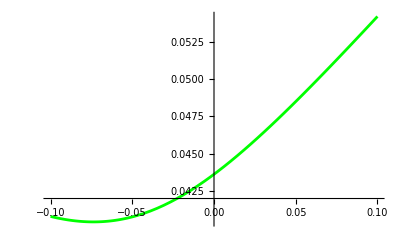

```mathematica
Module[{f=0.01,
α=0.0435,
ρ=0.5,
ν=0.3798,
K=0.0418,
T=3,printflag=0},
Plot[{SABRNormalVol[f,K,T,α,ρ,ν,printflag]},{K,-0.1,0.1},
PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]}},PlotLegend->{"SABR Normal"},LegendPosition->{1,1}]]
```

```mathematica
Application  Formule SABR usuelle
```

```mathematica
SABRUsuelPlus6VolNormal[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b0,b1,b2,b3,b4,bz,favg,zavg,intrinsec,I0,I1,I2,call,result},
If[Abs[β-1]<0.01,z=(Log[f]-Log[K])/α+((-Log[f]^2+Log[K]^2) (β-1))/(2 α)+((Log[f]^3-Log[K]^3) (β-1)^2)/(6 α),
z=((f)^(1-β) -(K)^(1-β))/(α  (1-β))];
favg=f;
b0=(K)^β;
b1=β/K;
b2=β(β-1)/(K^2);
bz=(f)^β;
SABRgenericNormalVol[f,K,z,b0,b1,b2,bz,T,0,α,ρ,ν,printflag]
]
```

```mathematica
SABRUsuelPlus6VolNormal2[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b0,b1,b2,b3,b4,bz,favg,zavg,intrinsec,I0,I1,I2,call,result},
If[Abs[β-1]<0.01,z=(Log[f]-Log[K])/α+((-Log[f]^2+Log[K]^2) (β-1))/(2 α)+((Log[f]^3-Log[K]^3) (β-1)^2)/(6 α),
z=((f)^(1-β) -(K)^(1-β))/(α  (1-β))];
favg=f;
b0=(K)^β;
b1=β/K;
b2=β(β-1)/(K^2);
b3=β(β-1)(β-2)/(K^3);
b4=β(β-1)(β-2)(β-3)/(K^4);
bz=(f)^β;
SABRgenericNormalVol[f,K,z,b0,b1,b2,b3,b4,bz,T,0,α,ρ,ν,printflag]
]
```

```mathematica
SABRUsuelPlus6Option[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b0,b1,b2,b3,b4,bz,favg,zavg,intrinsec,I0,I1,I2,call,result},
If[Abs[β-1]<0.01,z=(Log[f]-Log[K])/α+((-Log[f]^2+Log[K]^2) (β-1))/(2 α)+((Log[f]^3-Log[K]^3) (β-1)^2)/(6 α),
z=((f)^(1-β) -(K)^(1-β))/(α  (1-β))];
favg=f;
b0=(K)^β;
b1=β/K;
b2=β(β-1)/(K^2);
bz=(f)^β;
SABRgenericOption[f,K,z,b0,b1,b2,bz,T,0,α,ρ,ν,printflag]
]
```

```mathematica
SABRUsuelPlus6Option2[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b0,b1,b2,b3,b4,bz,favg,zavg,intrinsec,I0,I1,I2,call,result},
If[Abs[β-1]<0.01,z=(Log[f]-Log[K])/α+((-Log[f]^2+Log[K]^2) (β-1))/(2 α)+((Log[f]^3-Log[K]^3) (β-1)^2)/(6 α),
z=((f)^(1-β) -(K)^(1-β))/(α  (1-β))];
favg=f;
b0=(K)^β;
b1=β/K;
b2=β(β-1)/(K^2);
b3=β(β-1)(β-2)/(K^3);
b4=β(β-1)(β-2)(β-3)/(K^4);
bz=(f)^β;
SABRgenericOption[f,K,z,b0,b1,b2,b3,b4,bz,T,0,α,ρ,ν,printflag]
]
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=0.6,
ρ=-0.1819,
ν=0.3798,T=10,printflag=0,K=0.05},
{SABRUsuelPlus6Option[f,K,T,α,β,ρ,ν,printflag],SABRUsuelPlus6Option2[f,K,T,α,β,ρ,ν,printflag],SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,printflag][[2]]}]
```

{0.00117542,0.00117636,0.00588416}

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1.3,
ρ=-0.1819,
ν=0.3798,
K=0.04,
T=4,printflag=0,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic"},
op=SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T];
Print["op=",op];
{SABRUsuelPlus6VolNormal[f,K,T,α,β,ρ,ν,printflag],NormalImplicitVol[f,K,T,op[[2]]]}]
```

op={0.0207882620291890724318551300579,0.00192649}

{0.000823729,0.00219478}

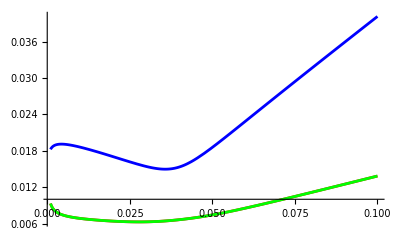

```mathematica
Module[{f=0.0418,
α=0.0435,
β=.7,
ρ=0.1819,
ν=0.3798,
K=0.0418,
T=35,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",printflag=0},
Plot[{SABRUsuelPlus6VolNormal[f,K,T,α,β,ρ,ν,printflag],SABRUsuelPlus6VolNormal2[f,K,T,α,β,ρ,ν,printflag],NormalImplicitVol[f,K,T,SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T][[2]]]},{K,0.001,0.1},
PlotStyle->{{Thickness[0.005],RGBColor[1,0,0]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[0,0.,1]}},PlotLegend->{"SABR Normal6","SABR Normal6-2","SABR Analytic"},LegendPosition->{1,1}]]
```

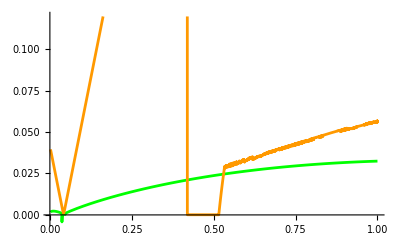

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1.4,
ρ=-0.1819,
ν=0.3798,
K=0.0418,
T=4,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",printflag=0},
Plot[{SABRUsuelPlus6VolNormal[f,K,T,α,β,ρ,ν,printflag],NormalImplicitVol[f,K,T,SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T][[2]]]},{K,0.002,1},
PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"SABR Normal","SABR Analytic","Hagan"},LegendPosition->{1,1}]]
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1.4,
ρ=-0.1819,
ν=0.3798,
K=0.0418,
T=4,method="SABR Type Analytic",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",printflag=0},
Plot[{SABRUsuelPlus6VolNormal[f,K,T,α,β,ρ,ν,printflag],NormalImplicitVol[f,K,T,SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T][[2]]]},{K,0.001,0.03},
PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"SABR Normal","SABR Analytic","Hagan"},LegendPosition->{1,1}]]
```

⁃Graphics⁃

```mathematica
Normal Extended SABR
```

```mathematica
Clear[x,I0,z]
```

```mathematica
x[z_]:=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν
```

```mathematica
I0[z_]:=√(1-2 ν ρ z+ν^2 z^2)
```

```mathematica
favg[f_]:=f
```

```mathematica
(*         ∫_K^f 1/C[s] ⅆs->ϵ α z,C[f]->B[ϵ α z]           *)
```

```mathematica
z[f_]:=1/α∫_K^f 1/C[s] ⅆs
```

```mathematica
(*              theta[f_]:=Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K)]+1/4 ρ ν α C'[K] z[favg[f]]^2     *)
```

```mathematica
SigAdjust=Simplify[Normal[Series[((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2,{f,K,2}]],C[K]>0]
```

-1/(2880 α^2 C[K]^2)(T ((f-K)^2 (ν^4 (104-600 ρ^2+495 ρ^4)-60 α ν^3 ρ C'[K]+10 α^2 ν^2 (4-39 ρ^2) C'[K]^2+60 α^3 ν ρ C'[K]^3-α^4 C'[K]^4)+4 (f-K) α C[K] (α^2 C'[K]^2 (-30 ν ρ+(f-K) α C''[K])-30 α ν ρ C'[K] (-6 ν ρ+(f-K) α C''[K])+5 ν^2 (18 ν ρ (-1+ρ^2)+(f-K) α (-4+3 ρ^2) C''[K]))+4 α^2 C[K]^2 (30 α^2 C'[K]^2+60 (f-K) α ν ρ C''[K]-(f-K)^2 α^2 C''[K]^2-3 α C'[K] (60 ν ρ+(f-K)^2 α C^(3)[K])+30 ν (ν (-2+3 ρ^2)+(f-K)^2 α ρ C^(3)[K]))-12 α^4 C[K]^3 (20 C''[K]+(f-K) (10 C^(3)[K]+3 (f-K) C^(4)[K]))))

```mathematica
Collect[Simplify[Simplify[Normal[Series[(f-K)/x[z[f]] Exp[SigAdjust],{f,K,2}]],C[K]>0]/. {C[K]->b0,C'[K]->b0 b1,C''[K]->b0 b2,Derivative[3][C][K]->b0 b3,Derivative[4][C][K]->b0 b4,Derivative[5][C][K]->0,Derivative[6][C][K]->0}],T]
```

1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) (5760 b0 α+2880 b0 b1 (f-K) α-480 b0 b1^2 (f-K)^2 α+960 b0 b2 (f-K)^2 α-2880 (f-K) ν ρ+(480 (f-K)^2 ν^2 (2-3 ρ^2))/(b0 α)))+1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) T^2 (5 b0^5 b3^2 (f-K)^2 α^5+10 b0^4 (b1^2-2 b2) b3 (f-K)^2 α^4 ν ρ+5 b0^3 b1^4 (f-K)^2 α^3 ν^2 ρ^2-20 b0^3 b1^2 b2 (f-K)^2 α^3 ν^2 ρ^2+20 b0^3 b2^2 (f-K)^2 α^3 ν^2 ρ^2-60 b0^3 b1 b3 (f-K)^2 α^3 ν^2 ρ^2-60 b0^2 b1 (b1^2-2 b2) (f-K)^2 α^2 ν^3 ρ^3-180 b1 (f-K)^2 ν^5 ρ^3+180 b1 (f-K)^2 ν^5 ρ^5-30 b0^2 b3 (f-K)^2 α^2 ν^3 ρ (-1+ρ^2)+60 b0 b2 (f-K)^2 α ν^4 ρ^2 (-1+ρ^2)+(45 (f-K)^2 ν^6 ρ^2 (-1+ρ^2)^2)/(b0 α)+30 b0 b1^2 (f-K)^2 α ν^4 ρ^2 (1+5 ρ^2)))+1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) T (240 b0^3 b3 (f-K) α^3+2 b0^3 b1^4 (f-K)^2 α^3-8 b0^3 b1^2 b2 (f-K)^2 α^3+8 b0^3 b2^2 (f-K)^2 α^3+144 b0^3 b1 b3 (f-K)^2 α^3+72 b0^3 b4 (f-K)^2 α^3+240 b0^2 (b1^2-2 b2) (f-K) α^2 ν ρ-360 b0^2 b3 (f-K)^2 α^2 ν ρ+480 b1 (f-K)^2 ν^3 ρ-1440 b0 b1 (f-K) α ν^2 ρ^2+360 b1 (f-K)^2 ν^3 ρ^3-720 (f-K) ν^3 ρ (-1+ρ^2)-20 b0 b1^2 (f-K)^2 α ν^2 (4+3 ρ^2)+40 b0 b2 (f-K)^2 α ν^2 (4+3 ρ^2)-(2 (f-K)^2 ν^4 (104-420 ρ^2+315 ρ^4))/(b0 α)))

```mathematica
(f-K)/x[z[f]](1+((Log[α  √(C[K] C[f]) ( √I0[z[f]])x[z[f]]/(f-K) ]+1/4 ρ ν α C'[K] z[favg[f]]^2)T)/x[z[f]]^2) /.  {C[K]->b0,C'[K]->b0 b1,C''[K]->b0 b2,Derivative[3][C][K]->b0 b3,∫_K^f 1/C[s] ⅆs->α z,C[f]->bz}
```

((f-K) ν (1+(T ν^2 (1/4 b0 b1 z^2 α ν ρ+Log[(√(b0 bz) α (1+z^2 ν^2-2 z ν ρ)^(1/4) Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)])/((f-K) ν)]))/(Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)]^2)))/Log[(z ν-ρ+√(1+z^2 ν^2-2 z ν ρ))/(1-ρ)]

```mathematica
SABRgenericNormalVol2[f_,K_,z_,b0_,b1_,b2_,b3_,b4_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{x,σN,Q,ratio},
If[printflag>0,Print["SABRgenericNormalVol2:K=",K," z=",z," b0=",b0," b1=",b1," b2=",b2," b3=",b3," b4=",b4," bz=",bz," μ=",μ," α=",α," ρ=",ρ," ν=",ν]];
If[Abs[f-K]<0.01f,
(* development a la monnaie *)
σN=1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) (5760 b0 α+2880 b0 b1 (f-K) α-480 b0 b1^2 (f-K)^2 α+960 b0 b2 (f-K)^2 α-2880 (f-K) ν ρ+(480 (f-K)^2 ν^2 (2-3 ρ^2))/(b0 α)))+1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) T^2 (5 b0^5 b3^2 (f-K)^2 α^5+10 b0^4 (b1^2-2 b2) b3 (f-K)^2 α^4 ν ρ+5 b0^3 b1^4 (f-K)^2 α^3 ν^2 ρ^2-20 b0^3 b1^2 b2 (f-K)^2 α^3 ν^2 ρ^2+20 b0^3 b2^2 (f-K)^2 α^3 ν^2 ρ^2-60 b0^3 b1 b3 (f-K)^2 α^3 ν^2 ρ^2-60 b0^2 b1 (b1^2-2 b2) (f-K)^2 α^2 ν^3 ρ^3-180 b1 (f-K)^2 ν^5 ρ^3+180 b1 (f-K)^2 ν^5 ρ^5-30 b0^2 b3 (f-K)^2 α^2 ν^3 ρ (-1+ρ^2)+60 b0 b2 (f-K)^2 α ν^4 ρ^2 (-1+ρ^2)+(45 (f-K)^2 ν^6 ρ^2 (-1+ρ^2)^2)/(b0 α)+30 b0 b1^2 (f-K)^2 α ν^4 ρ^2 (1+5 ρ^2)))+1/5760(ⅇ^(-1/24 T (b0^2 (b1^2-2 b2) α^2-6 b0 b1 α ν ρ+ν^2 (-2+3 ρ^2))) T (240 b0^3 b3 (f-K) α^3+2 b0^3 b1^4 (f-K)^2 α^3-8 b0^3 b1^2 b2 (f-K)^2 α^3+8 b0^3 b2^2 (f-K)^2 α^3+144 b0^3 b1 b3 (f-K)^2 α^3+72 b0^3 b4 (f-K)^2 α^3+240 b0^2 (b1^2-2 b2) (f-K) α^2 ν ρ-360 b0^2 b3 (f-K)^2 α^2 ν ρ+480 b1 (f-K)^2 ν^3 ρ-1440 b0 b1 (f-K) α ν^2 ρ^2+360 b1 (f-K)^2 ν^3 ρ^3-720 (f-K) ν^3 ρ (-1+ρ^2)-20 b0 b1^2 (f-K)^2 α ν^2 (4+3 ρ^2)+40 b0 b2 (f-K)^2 α ν^2 (4+3 ρ^2)-(2 (f-K)^2 ν^4 (104-420 ρ^2+315 ρ^4))/(b0 α))),
(* cas normal *)
Q=√(1+z^2 ν^2-2 z ν ρ);

x=1/ν Log[(z ν-ρ+Q)/(1-ρ)];
ratio=x/(f-K);
If[printflag>0,Print["Q=",Q," x/(f-K)=",ratio," coef en T =",(1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]])/x^2 ]];

σN=Abs[ ((f-K)  Exp[(T  (1/4 b0 b1 z^2 α ν ρ+Log[Abs[(√(Q b0 bz) α  x)/(f-K)]]))/x^2])/x]]]
```

```mathematica
SABRgenericNormalOption2[f_,K_,z_,b0_,b1_,b2_,b3_,b4_,bz_,T_,μ_,α_,ρ_,ν_,printflag_]:=Module[{σN},
σN=SABRgenericNormalVol2[f,K,z,b0,b1,b2,b3,b4,bz,T,μ,α,ρ,ν,printflag];
If[printflag>0,Print["SABRgenericNormalOption2:σN=",σN]];
NormalCall[f,σN,K,T]]
```

```mathematica
Ca marche
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=1,
ρ=-0.1819,
ν=0.3798,
T=4,printflag=0},
Plot[{ImpVolBS[f,K,T,SABRUsuelPlus6Option[f,K,T,α,β,ρ,ν,printflag]]},{K,0.001,0.2}]]
```

⁃Graphics⁃

```mathematica
Ca casse pour les low strike
```

```mathematica
Module[{f=0.0418,
α=0.0435,
β=0.6,
ρ=-0.1819,
ν=0.3798,
T=30,printflag=0},
Plot[{SABRUsuelPlus6VolNormal[f,K,T,α,β,ρ,ν,printflag]},{K,0.0001,0.01}]]
```

⁃Graphics⁃

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=15,
TimeStepsNb=100,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.0001,0.0002,0.0005,0.001,0.0015,0.0017,0.002,0.0025,0.003,0.005,0.01,0.015,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};

AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0.0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];
AnalyticalSABRVol3=Table[SABRHaganVol[F1,strikelist[[i]],α1,β1,ρ1,ν1,T],{i,1,Length[strikelist]}];
AnaInterpolation3=Interpolation[Transpose[{strikelist,AnalyticalSABRVol3}]];
AnalyticalSABRVol4=Table[ImpVolBS[F1,strikelist[[i]],T,SABRUsuelPlus6Option[F1,strikelist[[i]],T,α1,β1,ρ1,ν1,0]],{i,1,Length[strikelist]}];
AnaInterpolation4=Interpolation[Transpose[{strikelist,AnalyticalSABRVol3}]];
AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];
Plot[{AnaInterpolation[x],AnaInterpolation2[x],AnaInterpolation3[x],AnaInterpolation4[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->{0,1},PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[0,0.5,10.8]}},PlotLegend->{"Simplified","Generic","Hagan","NomalGeneric"},LegendPosition->{1,1}]
]]
```

{1.937 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=15,
TimeStepsNb=100,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.0001,0.0002,0.0005,0.0007,0.001,0.0015,0.0017,0.002,0.0025,0.003,0.005,0.01,0.015};

AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0.0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];
AnalyticalSABRVol3=Table[SABRHaganVol[F1,strikelist[[i]],α1,β1,ρ1,ν1,T],{i,1,Length[strikelist]}];
AnaInterpolation3=Interpolation[Transpose[{strikelist,AnalyticalSABRVol3}]];
AnalyticalSABRVol4=Table[ImpVolBS[F1,strikelist[[i]],T,SABRUsuelPlus6Option[F1,strikelist[[i]],T,α1,β1,ρ1,ν1,0]],{i,1,Length[strikelist]}];
AnaInterpolation4=Interpolation[Transpose[{strikelist,AnalyticalSABRVol3}]];
Print["Simplified=",AnalyticalSABRVol2];
Print["Hagan=",AnalyticalSABRVol3];
Print["Normalapprox=",AnalyticalSABRVol4];
AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];
Plot[{AnaInterpolation[x],AnaInterpolation2[x],AnaInterpolation3[x],AnaInterpolation4[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->{0,1},PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[0,0.5,0.3]}},PlotLegend->{"Simplified","Generic","Hagan","NomalGeneric"},LegendPosition->{1,1}]
]]
```

{2.328 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=20,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.001,0.002,0.003,0.005,0.007,0.01,0.015,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};

AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

AnalyticalSABRVol3=Table[SABRUsuelPlus6VolNormal[F1,strikelist[[i]],T,α1,β1,ρ1,ν1,0]/F1,{i,1,Length[strikelist]}];
AnaInterpolation3=Interpolation[Transpose[{strikelist,AnalyticalSABRVol3}]];

AnalyticalSABRVol4=Table[ImpVolBS[F1,strikelist[[i]],T,SABRUsuelPlus6Option[F1,strikelist[[i]],T,α1,β1,ρ1,ν1,0]],{i,1,Length[strikelist]}];
AnaInterpolation4=Interpolation[Transpose[{strikelist,AnalyticalSABRVol4}]];


Plot[{AnaInterpolation[x],AnaInterpolation2[x],AnaInterpolation3[x],AnaInterpolation4[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[0,0.5,0.5]}},PlotLegend->{"SABR","Simplified","Normal*F","Normal/LogNormal"},LegendPosition->{1,1}]
]]
```

{8.344 Second,⁃Graphics⁃}

```mathematica
Comparaison avec Monte Carlo
```

```mathematica
SABRGeneratePath[F_,α_,β_,ρ_,ν_,T_,TimeStepsNb_,dt_,printflag_]:=Module[{i,j,Fn=F,αn=α,W1,W2,C,sqdt=√dt},
C=dt{{1,ρ},{ρ,1}};
If[printflag>1,Print["C=",C // MatrixForm]];
Do[alea=Random[MultinormalDistribution[{0,0},C]];
If[printflag>2,Print["alea=",alea // MatrixForm]];
{W1,W2}=alea;
Fn*=Exp[αn Fn^(β-1)W1 -(αn^2 Fn^(2β-2))/2 dt];
αn*=Exp[ν W2-ν^2/2 dt];
,{i,1,TimeStepsNb}];
{Fn,αn}]
```

```mathematica
SABRGenerateAntitheticPath[F_,α_,β_,ρ_,ν_,T_,TimeStepsNb_,dt_,printflag_]:=Module[{i,j,Fn=F,αn=α,Fna=F,αna=α,W1,W2,C,sqdt=√dt},
C=dt{{1,ρ},{ρ,1}};
If[printflag>1,Print["C=",C // MatrixForm]];
Do[alea=Random[MultinormalDistribution[{0,0},C]];
If[printflag>2,Print["alea=",alea // MatrixForm]];
{W1,W2}=alea;
Fn*=Exp[αn Fn^(β-1)W1 -(αn^2 Fn^(2β-2))/2 dt];
αn*=Exp[ν W2 -ν^2/2 dt];

Fna*=Exp[-αna Fna^(β-1)W1 -(αna^2 Fna^(2β-2))/2 dt];
αna*=Exp[-ν W2 -ν^2/2 dt];
,{i,1,TimeStepsNb}];
{{Fn,αn},{Fna,αna},{Fn,αna},{Fna,αn}}]
```

```mathematica
Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
T=5,
TimeStepsNb=100,
dt,printflag=2
},
dt=T/TimeStepsNb;
SABRGenerateAntitheticPath[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,printflag]]
```

C=(1/20 | -0.009095
-0.009095 | 1/20)

{{0.0507574,0.0140545},{0.0258935,0.0654537},{0.0507574,0.0654537},{0.0258935,0.0140545}}

```mathematica
SABRGenerateSample[F1_,α1_,β1_,ρ1_,ν1_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k},Table[SABRGeneratePath[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,printflag],{k,1,nbSample}]]
```

```mathematica
SABRGenerateAntitheticSample[F1_,α1_,β1_,ρ1_,ν1_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k, samples},samples=Table[SABRGenerateAntitheticPath[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,printflag],{k,1,nbSample}];
Flatten[samples,1]]
```

```mathematica
SABRMonteCarloOption[F1_,α1_,β1_,ρ1_,ν1_,K_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples},
samples=SABRGenerateAntitheticSample[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,nbSample,printflag];
Sum[If[samples[[i,1]]-K≥0,samples[[i,1]]-K,0],{i,1,Length[samples]}]/Length[samples]]
```

```mathematica
SABRMonteCarloSmile[F1_,α1_,β1_,ρ1_,ν1_,StrikeList_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples,i,k},
samples=SABRGenerateAntitheticSample[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,nbSample,printflag];
Table[Sum[If[samples[[i,1]]-StrikeList[[k]]≥0,samples[[i,1]]-StrikeList[[k]],0],{i,1,Length[samples]}]/Length[samples],{k,1,Length[StrikeList]}]]
```

```mathematica
Application Numerique
```

```mathematica
Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
T=5,
TimeStepsNb=100,
dt,printflag=1,
nbSample=10
},
dt=T/TimeStepsNb;
SABRGenerateSample[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,nbSample,printflag]]
```

{{0.0412573,0.0288671},{0.0494487,0.0607899},{0.0247792,0.245654},{0.0464689,0.0357184},{0.0408207,0.0224939},{0.0331073,0.114801},{0.0505259,0.0863957},{0.0309291,0.00661064},{0.0297976,0.053222},{0.0283923,0.0739695}}

```mathematica
Timing[Module[{
F1=0.04,
α1=0.04,
β1=0.6,
ρ1=-0.2,
ν1=0.4,
T=1,
TimeStepsNb=200,
nbSample=1000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];
Print["MCcallprice=",Transpose[{strikelist,MCcallprice}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];
Print["MCcallprice2=",Transpose[{strikelist,MCcallprice2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];
Print["MCcallprice3=",Transpose[{strikelist,MCcallprice3}]];

AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

MCcallprice={{0.005,0.0350188},{0.01,0.0300188},{0.02,0.0200198},{0.03,0.0101208},{0.035,0.0056611},{0.04,0.00236387},{0.045,0.000681936},{0.05,0.00014262},{0.06,0.0000108467},{0.07,0},{0.08,0},{0.09,0},{0.1,0},{0.12,0}}

MCcallprice2={{0.005,0.0349963},{0.01,0.0299963},{0.02,0.0199998},{0.03,0.0101303},{0.035,0.00567195},{0.04,0.0023407},{0.045,0.000671103},{0.05,0.000147179},{0.06,4.47628×10^-6},{0.07,0},{0.08,0},{0.09,0},{0.1,0},{0.12,0}}

MCcallprice3={{0.005,0.0351461},{0.01,0.0301461},{0.02,0.0201464},{0.03,0.0102406},{0.035,0.005714},{0.04,0.00237267},{0.045,0.000732048},{0.05,0.000191024},{0.06,0.0000164342},{0.07,1.54011×10^-6},{0.08,0},{0.09,0},{0.1,0},{0.12,0}}

{455.578 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=3,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];


AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

General::unfl: Underflow occurred in computation. Plus…

General::stop: Further output of General :: "unfl" will be suppressed during this calculation. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.005. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.0096652. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.014753. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

{4486.91 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=5,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];


AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

General::unfl: Underflow occurred in computation. Plus…

General::stop: Further output of General :: "unfl" will be suppressed during this calculation. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.005. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.0096652. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.014753. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

{4501.44 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=10,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];


AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

{4459.38 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=15,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];


AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

General::unfl: Underflow occurred in computation. Plus…

General::stop: Further output of General :: "unfl" will be suppressed during this calculation. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.005. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.0096652. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.014753. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

{4451.67 Second,⁃Graphics⁃}

```mathematica
Timing[Module[{
F1=0.0418,
α1=0.0435,
β1=0.6,
ρ1=-0.1819,
ν1=0.3798,
K=0.04,
T=20,
TimeStepsNb=200,
nbSample=10000,
dt,printflag=0
},
dt=T/TimeStepsNb;
strikelist={0.005,0.01,0.02,0.03,0.035,0.04,0.045,0.05,0.06,0.07,0.08,0.09,0.10,.12};
MCcallprice=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice[[i]]],{i,1,Length[strikelist]}];
MCInterpolation=Interpolation[Transpose[{strikelist,MCimplicitvols}]];

MCcallprice2=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols2=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice2[[i]]],{i,1,Length[strikelist]}];
MCInterpolation2=Interpolation[Transpose[{strikelist,MCimplicitvols2}]];

MCcallprice3=SABRMonteCarloSmile[F1,α1,β1,ρ1,ν1,strikelist,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitvols3=Table[ImpVolBS[F1,strikelist[[i]],T,1,MCcallprice3[[i]]],{i,1,Length[strikelist]}];
MCInterpolation3=Interpolation[Transpose[{strikelist,MCimplicitvols3}]];


AnalyticalSABRVol=Table[SimplifiedSABROption[F1,α1,β1,ρ1,ν1,strikelist[[i]],T,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation=Interpolation[Transpose[{strikelist,AnalyticalSABRVol}]];


AnalyticalSABRVol2=Table[SABRUsuelPlus5[F1,strikelist[[i]],T,0,α1,β1,ρ1,ν1,0][[1]],{i,1,Length[strikelist]}];
AnaInterpolation2=Interpolation[Transpose[{strikelist,AnalyticalSABRVol2}]];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],AnaInterpolation[x],AnaInterpolation2[x]},{x,Min[strikelist],Max[strikelist]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0.4,0.6,0]},{Thickness[0.005],RGBColor[0.2,0.6,0.2]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC","MC2","MC3","SABR","Simplified"},LegendPosition->{1,1}]
]]
```

General::unfl: Underflow occurred in computation. Plus…

General::stop: Further output of General :: "unfl" will be suppressed during this calculation. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.005. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.0096652. Plus…

Plot::plnr: MCInterpolation[x] is not a machine-size real number at x = 0.014753. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

{4444.26 Second,⁃Graphics⁃}

```mathematica
Verification of the differential equation
```

```mathematica
SABRHaganOption[{f_,α_,β_,ρ_,ν_,K_,T_}]:= SABRHaganOption[f,K,α,β,ρ,ν,T]
```

```mathematica
SabrApplyShock[args_,chocs_]:=Module[{S,α,β,ρ,ν,K,T,deltaS1,deltaα1},
{S,α,β,ρ,ν,K,T}=args;
{deltaS1,deltaα1}=chocs;
{S+deltaS1,α+deltaα1,β,ρ,ν,K,T}
]
```

```mathematica
SABRDerivative[args_,i_]:=Module[
{shift=0.0001,shock1moins,shock1plus,shock2moins,shock2plus,delplus,delmoins},
shock1moins={0,0};shock1moins[[i]]=-shift/2;
shock1plus={0,0};shock1plus[[i]]=shift/2;
delplus=SABRHaganOption[SabrApplyShock[args,shock1plus]];
delmoins=SABRHaganOption[SabrApplyShock[args,shock1moins]];
(delplus-delmoins)/shift
]
```

```mathematica
SABRDerivative[args_,i_,j_]:=Module[
{shift=0.0001,shock1moins,shock1plus,shock2moins,shock2plus,delplus,delmoins},
shock1moins={0,0};shock1moins[[i]]=-shift/2;
shock1plus={0,0};shock1plus[[i]]=shift/2;
shock2moins={0,0};shock2moins[[j]]=-shift/2;
shock2plus={0,0};shock2plus[[j]]=shift/2;
delplus=SABRHaganOption[SabrApplyShock[SabrApplyShock[args,shock1plus],shock2plus]]-
SABRHaganOption[SabrApplyShock[SabrApplyShock[args,shock1moins],shock2plus]];
delmoins=SABRHaganOption[SabrApplyShock[SabrApplyShock[args,shock1plus],shock2moins]]-
SABRHaganOption[SabrApplyShock[SabrApplyShock[args,shock1moins],shock2moins]];
(delplus-delmoins)/(shift^2)
]
```

```mathematica
SABROptionWithDrift[S_,α_,β_,ρ_,ν_,K_,T_]:=Module[{val},
dt=T/10;
shift=0.0001;
args={S,α,β,ρ,ν,K,T};
Ds1s1=SABRDerivative[args,1,1];
Ds1v1=SABRDerivative[args,1,2];
Dv1v1=SABRDerivative[args,2,2];
Print["Ds1s1=",Ds1s1];
terms1s1=1/2 α^2  S^(2β)Ds1s1;
terms1v1=α^2  ν ρ  S^β Ds1v1;
termv1v1=1/2 α^2  ν^2 Dv1v1;
Deltat=(SABRHaganOption[S,K,α,β,ρ,ν,T+dt/2]-
SABRHaganOption[S,K,α,β,ρ,ν,T-dt/2])/dt;

sum=terms1s1+terms1v1+termv1v1;
Print["sum=",sum,"  Deltat=",Deltat];
]
```

General::spell1: Possible spelling error: new symbol name "Deltat" is similar to existing symbol "deltat". Plus…

```mathematica
Module[{S=0.05,α=0.11,β=0.7,ρ=-0.5,ν=0.2,K=0.02,T=7},
SABROptionWithDrift[S,α,β,ρ,ν,K,T]
]
```

Ds1s1=2.82507

sum=0.000413141  Deltat=0.00045029

```mathematica
Essai pour ameliorer les performance long terme de la formule
```

```mathematica
Amelioration du comportement long terme de la formule generique
```

```mathematica
Clear[α,β,favg,f,K]
```

```mathematica
favg=K;
b1=β(favg)^(β-1);
b2=β(β-1)(favg)^(β-2)(favg)^β+b1^2;
```

```mathematica
I0=√(1+z  ν (z ν-2 ρ));I1=(z ν-ρ)/I0;I2=(1-ρ^2)/I0^3;
```

```mathematica
Simplify[((-3 b1^2 +2 b2) α^2+(2 I0 I2-I1^2) ν^2+(6 b1 α  )ν ρ)/8-1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2)) -(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(8 (1+z^2 ν^2-2 z ν ρ))]
```

0

```mathematica
Simplify[((-3 b1^2 +2 b2) α^2+(2 I0 I2-I1^2) ν^2+(6 b1 α  )ν ρ)/8-1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2)) ]
```

(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(8 (1+z^2 ν^2-2 z ν ρ))

```mathematica
Simplify[((-3 b1^2 +2 b2) α^2+(2 I0 I2-I1^2) ν^2+(6 b1 α  )ν ρ)/8-1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2)) +3/8 ν^2 I2 I0(I0^2-1)]
```

0

```mathematica
Simplify[((-3 b1^2 +2 b2) α^2+((3 I0^2-1) I0 I2-I1^2) ν^2+(6 b1 α  )ν ρ)/8-1/8 ((α^2 (-2+β) β K^(2 β))/K^2+(6 α β K^β ν ρ)/K+ν^2 (2-3 ρ^2)) ]
```

0

```mathematica
Simplify[(I1^2+2I0 I2)/8]
```

(2+z^2 ν^2-2 z ν ρ-ρ^2)/(8+8 z^2 ν^2-16 z ν ρ)

```mathematica
Simplify[((2 I0 I2-I1^2) ν^2)/8-(ν^2 (2-3 ρ^2))/8  ]
```

(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(8 (1+z^2 ν^2-2 z ν ρ))

```mathematica
Simplify[((2 I0 I2-I1^2) ν^2)/8 ]
```

-(ν^2 (-2+z^2 ν^2-2 z ν ρ+3 ρ^2))/(8 (1+z^2 ν^2-2 z ν ρ))

```mathematica
Simplify[(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(1+z^2 ν^2-2 z ν ρ)-(3 ν^2(-1+ρ^2)((1+z^2 ν^2-2 z ν ρ)-1))/(1+z^2 ν^2-2 z ν ρ)]
```

0

```mathematica
Simplify[(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(8(1+z^2 ν^2-2 z ν ρ))+3/8 ν^2(1-ρ^2)(1-1/I0^2)]
```

0

```mathematica
Simplify[1+z^2 ν^2-2 z ν ρ-z ν(z ν-2 ρ)]
```

1

```mathematica
I0=√(1+z  ν (z ν-2 ρ));I1=(z ν-ρ)/I0;I2=(1-ρ^2)/I0^3;
```

```mathematica
Simplify[(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/8+3/8 ν^2(1-ρ^2)(1-1/I0^2)]
```

(3 z^2 ν^4 (z ν-2 ρ)^2 (-1+ρ^2))/(8 (1+z^2 ν^2-2 z ν ρ))

```mathematica
SABRgeneric8[intrinsec_,z_,κb1_,κb2_,b1_,SqB0Bαz_,T_,μ_,α_,ρ_,ν_,printflag_]:=
Module[{x,I0,I1,I2,κ,f1overf0,xp},
x=Log[(-ρ+ν z+√(1-2 ν ρ z+ν^2 z^2))/(1-ρ)]/ν;(*  x    est la distance geodesique , on approxime la prob de transition par ⅇ^(-x^2/(2T))(1+..)  *)
If[printflag>0,Print["SABRgeneric8: z=",SetPrecision[z,12]," SqB0Bαz=",SetPrecision[SqB0Bαz,12]," κb1=",SetPrecision[κb1,12]," κb2=",SetPrecision[κb2,12]," b1=",SetPrecision[b1,12]]];
I0=√(1+z  ν (z ν-2 ρ));I1=(z ν-ρ)/I0;I2=(1-ρ^2)/I0^3;

κ=(12  μ+ (-3 κb1^2 +2 κb2) α^2-4 z^2 μ^2+((3 I0^2-1) I0 I2-I1^2) ν^2+(6 κb1 α -16 z μ )ν ρ)/8;
f1overf0=ⅇ^(((2 μ+b1 α  ν ρ) z^2)/4);

If[printflag>0,Print[" SABRgeneric8: f1overf0=",SetPrecision[f1overf0,12]," I0=",SetPrecision[I0,12]," κ=",SetPrecision[κ,12]," GIntegralAnalytical[√-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical[√-κ,Abs[x]/(√2),√T],12],
" GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]=",SetPrecision[GIntegralAnalytical2[-κ,Abs[x]/(√2),√T],12]," intrinsec=",intrinsec]];
If[printflag>0,Print["SABRgeneric8: (-3 κb1^2 +2 κb2) α^2=",SetPrecision[(-3 κb1^2 +2 κb2) α^2,12]," (2 I0 I2-I1^2) ν^2-(3 z SuperscriptBox[ν, 3] (z ν - 2 ρ) (-1 + SuperscriptBox[ρ, 2]))/(1 + SuperscriptBox[z, 2] SuperscriptBox[ν, 2] - 2 z ν ρ)=",SetPrecision[(2 I0 I2-I1^2) ν^2-(3 z ν^3 (z ν-2 ρ) (-1+ρ^2))/(1+z^2 ν^2-2 z ν ρ),12]," (6 b1 α -16 z μ )ν ρ=",SetPrecision[(6 b1 α -16 z μ )ν ρ,12]]];
intrinsec+α/2 √(2/π)SqB0Bαz  f1overf0 √I0 GIntegralAnalytical2[-κ,Abs[x]/(√2),√T]]
```

```mathematica
SABRUsuelPlus8[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{z,b1,b2,κb1,κb2,B0Bαz,favg,zavg,favgb1,zavgb1,intrinsec,I0,I1,I2,call,result},
z=((f)^(1-β) -(K)^(1-β))/(α  (1-β));
favg=(f+K)/2;
κb1=β(favg)^(β-1);
κb2=β(β-1)(favg)^(β-2)(favg)^β+κb1^2;
favgb1=(f+K)/2;
b1=β(favgb1)^(β-1);

B0Bαz=(K)^β(f)^β;
intrinsec=Max[f-K,0];
call=SABRgeneric8[intrinsec,z,κb1,κb2,b1,√B0Bαz,T,0,α,ρ,ν,printflag];
result={ImpVolBS[f,K,T,1,call],call};
result
]
```

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,ρ=-0.5,ν=0.3798,K=0.045,T=50,printflag=0},
{SABRUsuelPlus8[f,K,T,α,β,ρ,ν,printflag],SABRUsuelPlus5[f,K,T,0,α,β,ρ,ν,printflag],SABROptionAnalytic[f,α,β,ρ,ν,K,T,printflag],SABROptionAnalytic[f,α,β,ρ,ν,K,T]}]
```

{{0.130556435125332481012979191627,0.0138798},{0.130556435125332498245987173116,0.0138798},{0.130958373686095969023177891145,0.0139239},{0.1309583736860960617256975482,0.0139239}}

```mathematica
DigitaleSABRUsuelPlus8[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{shift=Max[Abs[f],Abs[K]]/100.,v1,v2},
v1=SABRUsuelPlus8[f,K-shift,T,α,β,ρ,ν,printflag][[2]];
v2=SABRUsuelPlus8[f,K+shift,T,α,β,ρ,ν,printflag][[2]];
-(v2-v1)/(2.shift)]
```

```mathematica
DigitaleSABRUsuelPlus5[f_,K_,T_,α_,β_,ρ_,ν_,printflag_]:=Module[{shift=Max[Abs[f],Abs[K]]/100.,v1,v2},
v1=SABRUsuelPlus5[f,K-shift,T,0,α,β,ρ,ν,printflag][[2]];
v2=SABRUsuelPlus5[f,K+shift,T,0,α,β,ρ,ν,printflag][[2]];
-(v2-v1)/(2.shift)]
```

```mathematica
Off[FindRoot::"precw"]
```

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,ρ=-0.5,ν=0.3798,K=0.045,T=50,printflag=0},
{DigitaleSABRUsuelPlus8[f,K,T,α,β,ρ,ν,printflag],DigitaleSABROptionAnalytic[f,α,β,ρ,ν,K,T,printflag]}]
```

{0.546088,0.533866}

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,ρ=-0.5,ν=0.3798,K=0.045,T=35,printflag=0},
Plot[{DigitaleSABRUsuelPlus8[f,K,T,α,β,ρ,ν,printflag],DigitaleSABRUsuelPlus5[f,K,T,α,β,ρ,ν,printflag],DigitaleSABROptionAnalytic[f,α,β,ρ,ν,K,T,printflag]},{K,0.002,0.2}]]
```

⁃Graphics⁃

```mathematica
Etudes du smile / correlation
```

```mathematica
Module[{f=0.0418,
α=0.0435,K,T=5,ρ1=0,ρ2=0.25,ρ3=0.4,ρ4=0.8,ρ5=0.95,β=0.7,ν=0.3},
Plot[{SABROptionAnalytic[f,α,β,ρ1,ν,K,T][[1]],SABROptionAnalytic[f,α,β,ρ2,ν,K,T][[1]],SABROptionAnalytic[f,α,β,ρ3,ν,K,T][[1]],SABROptionAnalytic[f,α,β,ρ4,ν,K,T][[1]],SABROptionAnalytic[f,α,β,ρ5,ν,K,T][[1]]},{K,0.005,0.3},PlotStyle->{{Thickness[0.005],RGBColor[1,0.,0]},{Thickness[0.005],RGBColor[0.,1,0.]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0.5,1]},{Thickness[0.005],RGBColor[0.5,0,1]}},PlotLegend->{"ρ="<>ToString[ρ1],"ρ="<>ToString[ρ2],"ρ="<>ToString[ρ3],"ρ="<>ToString[ρ4],"ρ="<>ToString[ρ5],"ρ="<>ToString[ρ5]},LegendPosition->{1,-0.5}]]
```

⁃Graphics⁃

```mathematica
Etudes du smile / maturité
```

```mathematica
Module[{f=0.0418,
α=0.0435,K,T1=5,T2=10,T3=20,T4=30,T5=50,β=0.7,ρ=-0.5,ν=0.3},
Plot[{SABROptionAnalytic[f,α,β,ρ,ν,K,T1][[1]],SABROptionAnalytic[f,α,β,ρ,ν,K,T2][[1]],SABROptionAnalytic[f,α,β,ρ,ν,K,T3][[1]],SABROptionAnalytic[f,α,β,ρ,ν,K,T4][[1]],SABROptionAnalytic[f,α,β,ρ,ν,K,T5][[1]]},{K,0.01,0.3},PlotStyle->{{Thickness[0.005],RGBColor[1,0.,0]},{Thickness[0.005],RGBColor[0.,1,0.]},{Thickness[0.005],RGBColor[0,0,1]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,0.5,1]},{Thickness[0.005],RGBColor[0.5,0,1]}},PlotLegend->{"T="<>ToString[T1],"T="<>ToString[T2],"T="<>ToString[T3],"T="<>ToString[T4],"T="<>ToString[T5],"T="<>ToString[T5]},LegendPosition->{1,1}]]
```

⁃Graphics⁃

```mathematica
Module[{f=0.0418,
α=0.0435,T1=2,T2=20,T3=50,β=0.7,ρ=-0.5,ν=0.3,K=0.05},
SABROptionDirect[f,α,β,ρ,ν,K,T1]]
```

{14.1421 call$5756318,call$5756318}

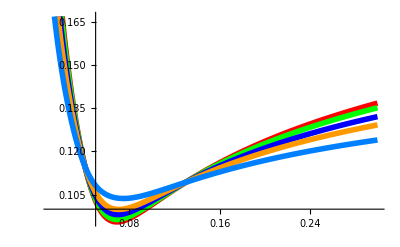

```mathematica
Module[{f=0.0418,
α=0.0435,K,T1=5,T2=10,T3=20,T4=30,T5=50,β=0.7,ρ=-0.5,ν=0.2},
Plot[{SABROptionDirect[f,α,β,ρ,ν,K,T1][[1]],SABROptionDirect[f,α,β,ρ,ν,K,T2][[1]],SABROptionDirect[f,α,β,ρ,ν,K,T3][[1]],SABROptionDirect[f,α,β,ρ,ν,K,T4][[1]],SABROptionDirect[f,α,β,ρ,ν,K,T5][[1]]},{K,0.01,0.3},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.005],RGBColor[0.5,0,1]}},PlotLegend->{"T="<>ToString[T1],"T="<>ToString[T2],"T="<>ToString[T3],"T="<>ToString[T4],"T="<>ToString[T5]},LegendPosition->{1,-0.5}]]
```

```mathematica
Module[{f=0.0418,
α=0.0435,K,T1=5,T2=10,T3=20,T4=30,T5=50,β=0.7,ρ=-0.5,ν=0.3},
Plot[{ SABRHaganVol[f,K,α,β,ρ,ν,T1], SABRHaganVol[f,K,α,β,ρ,ν,T2], SABRHaganVol[f,K,α,β,ρ,ν,T3], SABRHaganVol[f,K,α,β,ρ,ν,T4], SABRHaganVol[f,K,α,β,ρ,ν,T5]},{K,0.01,0.3},PlotStyle->{{Thickness[0.01],RGBColor[1,0.,0]},{Thickness[0.01],RGBColor[0.,1,0.]},{Thickness[0.01],RGBColor[0,0,1]},{Thickness[0.01],RGBColor[1,0.6,0]},{Thickness[0.01],RGBColor[0,0.5,1]},{Thickness[0.01],RGBColor[0.5,0,1]}},PlotLegend->{"T="<>ToString[T1],"T="<>ToString[T2],"T="<>ToString[T4],"T="<>ToString[T5],"T="<>ToString[T5]},LegendPosition->{1,-0.5}]]
```

⁃Graphics⁃

```mathematica
Etudes des derivées / ρ et ν
```

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,K1=0.038,K2=0.045,T=2,ρ,ν},
Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> out of the money T="<>ToString[T]];
Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> out of the money T="<>ToString[T]]]
```

⁃SurfaceGraphics⁃

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,K1=0.038,K2=0.045,T=10,ρ,ν},
Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> out of the money T="<>ToString[T]];
Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> out of the money T="<>ToString[T]]]
```

⁃SurfaceGraphics⁃

```mathematica
Module[{f=0.0418,
α=0.0435,β=0.7,K1=0.038,K2=0.045,T=30,ρ,ν},
Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalytic[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" α -> out of the money T="<>ToString[T]];
Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K1,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> in the money T="<>ToString[T]];Plot3D[SABROptionAnalyticFromATMVol[f,α,β,ρ,ν,K2,T][[1]],{ρ,-0.5,+0.5},{ν,0.3,0.4},PlotLabel->" σATM -> out of the money T="<>ToString[T]]]
```

⁃SurfaceGraphics⁃

```mathematica
Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ=-0.5,ν=0.2},K1=f+0.001;K2=f-0.001;
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]-SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]]
```

-0.003179364661257886190055454879

```mathematica
Clear[ShadowPlot3D]
```

```mathematica
<<"BarCharts`";<<"Histograms`"
```

```mathematica
Timing[Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ,ν=0.2},K1=f+0.001;K2=f-0.001;
Plot3D[
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]-SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]
,{ρ,-0.5,+0.5},{β,0.001,0.999},ViewPoint->{0,-2,0}]]]
```

{91.859 Second,⁃SurfaceGraphics⁃}

```mathematica
Timing[Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ,ν=0.2},K1=f+0.001;K2=f-0.001;
Plot3D[
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]-SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]
,{ρ,-0.5,+0.5},{β,0.001,0.999},ViewPoint->{0,-2,2}]]]
```

{95.531 Second,⁃SurfaceGraphics⁃}

```mathematica
Timing[Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ,ν=0.2},K1=f+0.001;K2=f-0.001;
Plot3D[
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]-SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]
,{ρ,-0.5,+0.5},{β,0.001,0.999},ViewPoint->{-2,1.5,0.5},PlotPoints->20,PlotRange->{-0.004,0.00225}]]]
```

{61. Second,⁃SurfaceGraphics⁃}

```mathematica
Timing[Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ,ν=0.2},K1=f+0.01;K2=f-0.01;K=f;
Plot3D[
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]+SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]-2SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K,T][[1]]
,{ρ,-0.5,+0.5},{β,0.001,0.999},ViewPoint->{-2,1.5,0.5}]]]
```

{156.578 Second,⁃SurfaceGraphics⁃}

```mathematica
Timing[Module[{f=0.0418,ATMvol=0.11,β=0.7,K1,K2,T=2,ρ,ν=0.2},K1=f+0.01;K2=f-0.01;K=f;
Plot3D[
SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K1,T][[1]]+SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K2,T][[1]]-2SABROptionAnalyticFromATMVol[f,ATMvol,β,ρ,ν,K,T][[1]]
,{ρ,-0.5,+0.5},{ν,0.1,2},ViewPoint->{2,1.5,1}]]]
```

{136.468 Second,⁃SurfaceGraphics⁃}

```mathematica
Monte Carlo Verification
```

```mathematica
MonoSABR : un facteur
```

```mathematica
SABRMonteCarloOption[F1_,α1_,β1_,ρ1_,ν1_,K_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples},samples=SABRGenerateAntitheticSample[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,nbSample,printflag];(∑_(i=1)^Length[samples] If[samples⟦i,1⟧-K≥0,samples⟦i,1⟧-K,0])/Length[samples]]
```

```mathematica
{{{{SABRMonteCarloSmile[F1_,α1_,β1_,ρ1_,ν1_,StrikeList_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{samples,i,k},samples=SABRGenerateAntitheticSample[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,nbSample,printflag];Table[(∑_(i=1)^Length[samples] If[samples⟦i,1⟧-StrikeList⟦k⟧≥0,samples⟦i,1⟧-StrikeList⟦k⟧,0])/Length[samples],{k,1,Length[StrikeList]}]]}}}}
```

```mathematica
{{{{SABRGenerateAntitheticSample[F1_,α1_,β1_,ρ1_,ν1_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k,samples},samples=Table[SABRGenerateAntitheticPath[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,printflag],{k,1,nbSample}];Flatten[samples,1]]}}}}
```

```mathematica
{{{{SABRGenerateSample[F1_,α1_,β1_,ρ1_,ν1_,T_,TimeStepsNb_,dt_,nbSample_,printflag_]:=Module[{k},Table[SABRGeneratePath[F1,α1,β1,ρ1,ν1,T,TimeStepsNb,dt,printflag],{k,1,nbSample}]]}}}}
```

```mathematica
{{{{SABRGenerateAntitheticPath[F_,α_,β_,ρ_,ν_,T_,TimeStepsNb_,dt_,printflag_]:=Module[{i,j,Fn=F,αn=α,Fna=F,αna=α,W1,W2,C,sqdt=√dt},C=dt {{1,ρ},{ρ,1}};If[printflag>1,Print["C=","MatrixForm"[C]]];Do[alea=Random[MultinormalDistribution[{0,0},C]];If[printflag>2,Print["alea=","MatrixForm"[alea]]];{W1,W2}=alea;Fn*=ⅇ^(αn Fn^(β-1) W1-1/2 (αn^2 Fn^(2 β-2)) dt);αn*=ⅇ^(ν W2-(ν^2 dt)/2);Fna*=ⅇ^(-αna Fna^(β-1) W1-1/2 (αna^2 Fna^(2 β-2)) dt);αna*=ⅇ^(-ν W2-(ν^2 dt)/2);,{i,1,TimeStepsNb}];{{Fn,αn},{Fna,αna},{Fn,αna},{Fna,αn}}]}}}}
```

```mathematica
{{{{SABRGeneratePath[F_,α_,β_,ρ_,ν_,T_,TimeStepsNb_,dt_,printflag_]:=Module[{i,j,Fn=F,αn=α,W1,W2,C,sqdt=√dt},C=dt {{1,ρ},{ρ,1}};If[printflag>1,Print["C=","MatrixForm"[C]]];Do[alea=Random[MultinormalDistribution[{0,0},C]];If[printflag>2,Print["alea=","MatrixForm"[alea]]];{W1,W2}=alea;Fn*=ⅇ^(αn Fn^(β-1) W1-1/2 (αn^2 Fn^(2 β-2)) dt);αn*=ⅇ^(ν W2-(ν^2 dt)/2);,{i,1,TimeStepsNb}];{Fn,αn}]}}}}
```

```mathematica
MCcallvalues3
```

{0.0201491,0.0151491,0.010224,0.00582036,0.00298033,0.00245161,0.00202309,0.000891311,0.000254036,0.0000932659,0.0000208657}

```mathematica
Timing[Module[{
F=0.0418,
α=0.0435,
β=0.6,
ρ=-0.1819,
ν=0.3798,
StrikeList,
T=1,
TimeStepsNb=20,
nbSample=5000,
dt,callvalues,implicitNormalvols,printflag=0
},StrikeList={-0.02,-0.015,-0.01,-0.005,-0.001,0,0.001,0.0050,0.01,0.015,0.02}+F;
dt=T/TimeStepsNb;
MCcallvalues=SABRMonteCarloSmile[F,α,β,ρ,ν,StrikeList,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitNormalvols=Table[NormalImplicitVol[F,StrikeList[[i]],T,MCcallvalues[[i]]],{i,1,Length[StrikeList]}];
MCInterpolation=Interpolation[Transpose[{StrikeList,MCimplicitNormalvols}]];
MCgraph=Plot[MCInterpolation[x],{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[1,0,0]}}];

MCcallvalues2=SABRMonteCarloSmile[F,α,β,ρ,ν,StrikeList,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitNormalvols2=Table[NormalImplicitVol[F,StrikeList[[i]],T,MCcallvalues2[[i]]],{i,1,Length[StrikeList]}];
MCInterpolation2=Interpolation[Transpose[{StrikeList,MCimplicitNormalvols2}]];
MCgraph=Plot[MCInterpolation2[x],{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[1,0.2,0]}}];

MCcallvalues3=SABRMonteCarloSmile[F,α,β,ρ,ν,StrikeList,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitNormalvols3=Table[NormalImplicitVol[F,StrikeList[[i]],T,MCcallvalues3[[i]]],{i,1,Length[StrikeList]}];
MCInterpolation3=Interpolation[Transpose[{StrikeList,MCimplicitNormalvols3}]];
MCgraph3=Plot[MCInterpolation3[x],{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[1,0,0.5]}}];

MCcallvalues4=SABRMonteCarloSmile[F,α,β,ρ,ν,StrikeList,T,TimeStepsNb,dt,nbSample,printflag];
MCimplicitNormalvols4=Table[NormalImplicitVol[F,StrikeList[[i]],T,MCcallvalues4[[i]]],{i,1,Length[StrikeList]}];
MCInterpolation4=Interpolation[Transpose[{StrikeList,MCimplicitNormalvols4}]];
MCgraph4=Plot[MCInterpolation4[x],{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[1,0.5,0]}}];

Analyticcallvalues=Table[SABROptionHagan[F,α,β,ρ,ν,StrikeList[[i]],T][[2]],{i,1,Length[StrikeList]}];
AnalyticalimplicitNormalvols=Table[NormalImplicitVol[F,StrikeList[[i]],T,Analyticcallvalues[[i]]],{i,1,Length[StrikeList]}];
AnalyticalInterpolation=Interpolation[Transpose[{StrikeList,AnalyticalimplicitNormalvols}]];
Analyticalgraph=Plot[AnalyticalInterpolation[x],{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[0,1,0]}}];

Plot[{MCInterpolation[x],MCInterpolation2[x],MCInterpolation3[x],MCInterpolation4[x],AnalyticalInterpolation[x]},{x,Min[StrikeList],Max[StrikeList]},PlotRange->All,PlotStyle->{{Thickness[0.005],RGBColor[1,0,0]},{Thickness[0.005],RGBColor[1,0.3,0]},{Thickness[0.005],RGBColor[1,0,0.5]},{Thickness[0.005],RGBColor[1,0.6,0]},{Thickness[0.005],RGBColor[0,1,0]},{Thickness[0.005],RGBColor[0,0,1]}},PlotLegend->{"MC 1","MC 2","MC 3","MC 4","SABR"}]
]]
```

{253.032 Second,⁃Graphics⁃}

```mathematica
Fonctions pour analyser des cas avec traitemen symbolique des derivées
```

```mathematica
BS1[f_,k_,t_,v_]:=f NormalDis[(Log[f/k]+(v^2 t)/2)/(v √t)]-k NormalDis[(Log[f/k]-(v^2 t)/2)/(v √t)]
```

```mathematica
SABRFromATMVolToAlpha[f_,ATMVol_,β_,ρ_,ν_,{method_,zmethod_,zetamethod_,favmethod_},K_,T_]:=Module[{α,ss},
Print[SABROption[f,0.2,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T][[1]]]
ss=FindRoot[SABROption[f,α,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T][[1]]==ATMVol,{α,0.2,0.0001,15.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss]
```

```mathematica
Module[{ATMVol=0.15,β=0.7,ρ=-0.5,ν=0.2,method="Directe",zmethod="Exact",zetamethod="Exact",favmethod="Arithmetic",f=0.05,K=0.04,T=1},SABRFromATMVolToAlpha[f,ATMVol,β,ρ,ν,{method,zmethod,zetamethod,favmethod},K,T]]
```

FindRoot::nlnum: The function value {-0.15 + sig$9708} is not a list of numbers with dimensions {1} at {α$9707} = {0.2}. More…

0.516193

Set::write: Tag Times in Null\ ss$9707 is Protected. More…

FindRoot::nlnum: The function value {-0.15 + sig$9712} is not a list of numbers with dimensions {1} at {α$9707} = {0.2}. More…

ss$9707

```mathematica
ComparePlotVolCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{Kmin_,Kmax_},T_]:=Module[{},
Plot[
{SABROption[f,α,β,ρ,ν,Meth1,K,T][[1]],SABROption[f,α,β,ρ,ν,Meth2,K,T][[1]]}
,{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotLegend->{name1,name2},LegendPosition->{1,0},AxesLabel->{"Strike","Vol"}]];
```

```mathematica
ComparePlotVolCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{name3_,Meth3_},{Kmin_,Kmax_},T_]:=Module[{},
Plot[
{SABROption[f,α,β,ρ,ν,Meth1,K,T][[1]],SABROption[f,α,β,ρ,ν,Meth2,K,T][[1]],SABROption[f,α,β,ρ,ν,Meth3,K,T][[1]]}
,{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},PlotLegend->{name1,name2,name3},LegendPosition->{1,0},AxesLabel->{"Strike","Vol"}]];
```

```mathematica
ComparePlotDigitalCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{Kmin_,Kmax_},T_]:=Block[{},
SABRdistr1=DerKSABROption[Meth1];
SABRdistr2=DerKSABROption[Meth2];
Plot[
{-SABRdistr1[f,α,β,ρ,ν,K,T],-SABRdistr2[f,α,β,ρ,ν,K,T]},{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotLegend->{name1,name2},LegendPosition->{1,0},AxesLabel->{"Strike","Digitale"}]];
```

```mathematica
ComparePlotDigitalCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{name3_,Meth3_},{Kmin_,Kmax_},T_]:=Block[{},
SABRdistr1=DerKSABROption[Meth1];
SABRdistr2=DerKSABROption[Meth2];
SABRdistr3=DerKSABROption[Meth3];
Plot[
{-SABRdistr1[f,α,β,ρ,ν,K,T],-SABRdistr2[f,α,β,ρ,ν,K,T],-SABRdistr3[f,α,β,ρ,ν,K,T]},{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},PlotLegend->{name1,name2,name3},LegendPosition->{1,0},AxesLabel->{"Strike","Digitale"}]];
```

```mathematica
ComparePlotDigitalCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{name3_,Meth3_},{name4_,Meth4_},{Kmin_,Kmax_},T_]:=Block[{},
SABRdistr1=DerKSABROption[Meth1];
SABRdistr2=DerKSABROption[Meth2];
SABRdistr3=DerKSABROption[Meth3];
SABRdistr4=DerKSABROption[Meth4];
Plot[
{-SABRdistr1[f,α,β,ρ,ν,K,T],-SABRdistr2[f,α,β,ρ,ν,K,T],-SABRdistr3[f,α,β,ρ,ν,K,T],-SABRdistr4[f,α,β,ρ,ν,K,T]},{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.5,0.5,0]},PlotLegend->{name1,name2,name3,name4},LegendPosition->{1,0},AxesLabel->{"Strike","Digitale"}]];
```

```mathematica
ComparePlotDigitalCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{name3_,Meth3_},{name4_,Meth4_},{name5_,Meth5_},{Kmin_,Kmax_},T_]:=Block[{},
SABRdistr1=DerKSABROption[Meth1];
SABRdistr2=DerKSABROption[Meth2];
SABRdistr3=DerKSABROption[Meth3];
SABRdistr4=DerKSABROption[Meth4];
SABRdistr5=DerKSABROption[Meth5];
Plot[
{-SABRdistr1[f,α,β,ρ,ν,K,T],-SABRdistr2[f,α,β,ρ,ν,K,T],-SABRdistr3[f,α,β,ρ,ν,K,T],-SABRdistr4[f,α,β,ρ,ν,K,T],-SABRdistr5[f,α,β,ρ,ν,K,T]},{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0.5,0.5,0],RGBColor[0.,0.5,0.5]},PlotLegend->{name1,name2,name3,name4,name5},LegendPosition->{1,0},AxesLabel->{"Strike","Digitale"}]];
```

```mathematica
ComparePlotDensityCase[f_,α_,β_,ρ_,ν_,{name1_,Meth1_},{name2_,Meth2_},{Kmin_,Kmax_},T_]:=Block[{},
SABRfunc1=SABRVol[f,α,β,ρ,ν,Meth1,K,T];
SABRfunc2=SABRVol[f,α,β,ρ,ν,Meth2,K,T];
SABRdens1=D[BS1[f,K,T,SABRfunc1],{K,2}];
SABRdens2=D[BS1[f,K,T,SABRfunc2],{K,2}];
Plot[
{SABRdens1,SABRdens2},{K,Kmin,Kmax},PlotRange->All,
PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]},PlotLegend->{name1,name2},LegendPosition->{1,0},AxesLabel->{"Strike","Density"}]];
```

```mathematica
Module[{f=0.05,α=0.11,β=0.7,ρ=-0.5,ν=0.2,kmin=0.001,kmax=0.15,T=1,
Meth1={"RQL",{"NormaleHagan","Geometric","Geometric","Geometric"}},
Meth2={"ARM",{"Directe","Exact","Exact","Arithmetic"}}
},
ComparePlotVolCase[f,α,β,ρ,ν,Meth1,Meth2,{kmin,kmax},T]]
```

⁃Graphics⁃

```mathematica
Module[{f=0.05,α=0.11,β=0.7,ρ=-0.5,ν=0.3,kmin=0.0001,kmax=0.1,T=10,
Meth1={"RQL",{"NormaleHagan","Geometric","Geometric","Geometric"}},
Meth2={"ARM",{"Directe","Exact","Exact","Arithmetic"}}},
ComparePlotDigitalCase[f,α,β,ρ,ν,Meth1,Meth2,{kmin,kmax},T]];
```

```mathematica
Module[{f=0.05,α=0.11,β=0.7,ρ=-0.5,ν=0.2,kmin=0.001,kmax=0.5,T=10,
Meth1={"RQL",{"NormaleHagan","Geometric","Geometric","Geometric"}},
Meth2={"ARM",{"Directe","Exact","Exact","Arithmetic"}}},
ComparePlotDensityCase[f,α,β,ρ,ν,Meth1,Meth2,{kmin,kmax},T]];
```

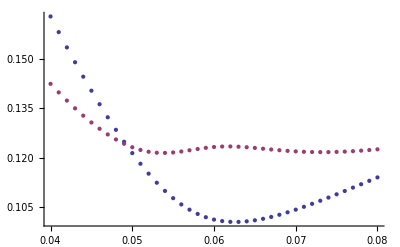
{-Graphics-,{{0.04,0.16284},{0.041,0.158092},{0.042,0.153465},{0.043,0.148961},{0.044,0.144585},{0.045,0.140339},{0.046,0.136233},{0.047,0.132275},{0.048,0.128476},{0.049,0.12485},{0.05,0.121414},{0.051,0.118186},{0.052,0.115186},{0.053,0.112435},{0.054,0.109953},{0.055,0.107757},{0.056,0.105859},{0.057,0.104266},{0.058,0.102976},{0.059,0.10198},{0.06,0.101263},{0.061,0.100805},{0.062,0.10058},{0.063,0.100562},{0.064,0.100726},{0.065,0.101046},{0.066,0.101499},{0.067,0.102065},{0.068,0.102726},{0.069,0.103466},{0.07,0.104271},{0.071,0.10513},{0.072,0.106033},{0.073,0.10697},{0.074,0.107937},{0.075,0.108925},{0.076,0.109931},{0.077,0.110949},{0.078,0.111978},{0.079,0.113012},{0.08,0.11405}}}

```mathematica
Module[{f=0.05,α=0.0248,T=17,β=0.5,ATMvol,ρ=-0.56,ν=0.45,lst,
Meth1={"NormaleHagan","Geometric","Geometric","Geometric",{Tanh,0.05,1.5}},
Meth2={"Directe","Exact","Exact","Arithmetic",{Tanh,0.05,1.5}}},
lst=Table[{K,SABROption[f,α,β,ρ,ν,Meth1,K,T][[1]]},{K,0.04,0.08,0.001}];
lst2=Table[{K,SABROption[f,α,β,ρ,ν,Meth2,K,T][[1]]},{K,0.04,0.08,0.001}];
{ListPlot[{lst,lst2}],lst}]
```